-Graphics- |  
Когнитивная визуализация 
Таранчук Валерий Борисович
БГУ, факультет прикладной математики и информатики

#### Учебные материалы, рекомендации пользователям СКА Mathematica, обучающие примеры и упражнения (оригинал документа создан NB, предоставляется студентам в формате PDF, конспект размещён на странице https://edufpmi.bsu.by/mod/lesson/....)

### Mathematica. Основы Wolfram Language prnPDF

Внимание!
По ходу занятия будут несколько контрольных вопросов/заданий (открываются по расписанию), 
отвечать на которые обязательно. Ответы учитываются в личном рейтинге. Баллы в рейтинг: 
указанный в экзаменаторе балл при правильном ответе, 0 - при неправильном ответе, -5 при отсутствии ответа.  
Сообщение об открытии задания (размещаются в разделе “Лекция NM”) будет мелодией и в общем чате.

-     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -    <  <  <  <         >  >  >  >  -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -

### Выложить. Код! forLect01.nb

## https://www.elib.bsu.by/browse?type=author&value=Таранчук%2C+В.+Б.&sort_by=2&order=ASC&rpp=100&etal=0&submit_browse=Обновить https://www.elib.bsu.by/browse?type=author&value=Taranchuk%2C+V.+B.&sort_by=2&order=ASC&rpp=30&etal=0&submit_browse=Обновить

```mathematica
(* Выложить. Код "Список встроенных функций и символов" *)  
names = Names["System`*"]; 
length[names] = Length[names]; 
i = 1; 
Pane[(Style[#1, 16, Darker[Blend[{Red, Green, Blue}, i++/length[names]]], 
     FontFamily -> "Arial"] & ) /@ names, {Full, 500}, Scrollbars -> {False, True}]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω,α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,ς,σ,τ,υ,φ,χ,ψ,ω,ϑ,ϒ,ϕ,ϖ,Ϛ,ϛ,Ϝ,ϝ,Ϟ,ϟ,Ϡ,ϡ,ϰ,ϱ,ϵ,AASTriangle,AbelianGroup,Abort,AbortKernels,AbortProtect,AbortScheduledTask,Above,Abs,AbsArg,AbsArgPlot,Absolute,AbsoluteCorrelation,AbsoluteCorrelationFunction,AbsoluteCurrentValue,AbsoluteDashing,AbsoluteFileName,AbsoluteOptions,AbsolutePointSize,AbsoluteThickness,AbsoluteTime,AbsoluteTiming,AcceptanceThreshold,AccountingForm,Accumulate,Accuracy,AccuracyGoal,ActionDelay,ActionMenu,ActionMenuBox,ActionMenuBoxOptions,Activate,Active,ActiveClassification,ActiveClassificationObject,ActiveItem,ActivePrediction,ActivePredictionObject,ActiveStyle,AcyclicGraphQ,AddOnHelpPath,AddSides,AddTo,AddToSearchIndex,AddUsers,AdjacencyGraph,AdjacencyList,AdjacencyMatrix,AdjustmentBox,AdjustmentBoxOptions,AdjustTimeSeriesForecast,AdministrativeDivisionData,AffineHalfSpace,AffineSpace,AffineStateSpaceModel,AffineTransform,After,AggregatedEntityClass,AggregationLayer,AircraftData,AirportData,AirPressureData,AirTemperatureData,AiryAi,AiryAiPrime,AiryAiZero,AiryBi,AiryBiPrime,AiryBiZero,AlgebraicIntegerQ,AlgebraicNumber,AlgebraicNumberDenominator,AlgebraicNumberNorm,AlgebraicNumberPolynomial,AlgebraicNumberTrace,AlgebraicRules,AlgebraicRulesData,Algebraics,AlgebraicUnitQ,Alignment,AlignmentMarker,AlignmentPoint,All,AllowAdultContent,AllowedCloudExtraParameters,AllowedCloudParameterExtensions,AllowedDimensions,AllowedFrequencyRange,AllowedHeads,AllowGroupClose,AllowIncomplete,AllowInlineCells,AllowKernelInitialization,AllowLooseGrammar,AllowReverseGroupClose,AllowScriptLevelChange,AllTrue,Alphabet,AlphabeticOrder,AlphabeticSort,AlphaChannel,AlternateImage,AlternatingFactorial,AlternatingGroup,AlternativeHypothesis,Alternatives,AltitudeMethod,AmbientLight,AmbiguityFunction,AmbiguityList,Analytic,AnatomyData,AnatomyForm,AnatomyPlot3D,AnatomySkinStyle,AnatomyStyling,AnchoredSearch,And,AndersonDarlingTest,AngerJ,AngleBisector,AngleBracket,AnglePath,AnglePath3D,AngleVector,AngularGauge,Animate,AnimationCycleOffset,AnimationCycleRepetitions,AnimationDirection,AnimationDisplayTime,AnimationRate,AnimationRepetitions,AnimationRunning,AnimationRunTime,AnimationTimeIndex,Animator,AnimatorBox,AnimatorBoxOptions,AnimatorElements,Annotate,Annotation,AnnotationDelete,AnnotationNames,AnnotationRules,AnnotationValue,Annuity,AnnuityDue,Annulus,AnomalyDetection,AnomalyDetectorFunction,Anonymous,Antialiasing,AntihermitianMatrixQ,Antisymmetric,AntisymmetricMatrixQ,Antonyms,AnyOrder,AnySubset,AnyTrue,Apart,ApartSquareFree,APIFunction,Appearance,AppearanceElements,AppearanceRules,AppellF1,Append,AppendCheck,AppendLayer,AppendTo,Apply,ApplySides,ArcCos,ArcCosh,ArcCot,ArcCoth,ArcCsc,ArcCsch,ArcCurvature,ARCHProcess,ArcLength,ArcSec,ArcSech,ArcSin,ArcSinDistribution,ArcSinh,ArcTan,ArcTanh,Area,Arg,ArgMax,ArgMin,ArgumentCountQ,ARIMAProcess,ArithmeticGeometricMean,ARMAProcess,Around,AroundReplace,ARProcess,Array,ArrayComponents,ArrayDepth,ArrayFilter,ArrayFlatten,ArrayMesh,ArrayPad,ArrayPlot,ArrayQ,ArrayResample,ArrayReshape,ArrayRules,Arrays,Arrow,Arrow3DBox,ArrowBox,Arrowheads,ASATriangle,Ask,AskAppend,AskConfirm,AskDisplay,AskedQ,AskedValue,AskFunction,AskState,AskTemplateDisplay,AspectRatio,AspectRatioFixed,Assert,AssociateTo,Association,AssociationFormat,AssociationMap,AssociationQ,AssociationThread,AssumeDeterministic,Assuming,Assumptions,AstronomicalData,AsymptoticDSolveValue,AsymptoticEqual,AsymptoticEquivalent,AsymptoticGreater,AsymptoticGreaterEqual,AsymptoticIntegrate,AsymptoticLess,AsymptoticLessEqual,AsymptoticOutputTracker,AsymptoticRSolveValue,AsymptoticSolve,AsymptoticSum,Asynchronous,AsynchronousTaskObject,AsynchronousTasks,Atom,AtomCoordinates,AtomCount,AtomDiagramCoordinates,AtomList,AtomQ,AttentionLayer,Attributes,Audio,AudioAmplify,AudioAnnotate,AudioAnnotationLookup,AudioBlockMap,AudioCapture,AudioChannelAssignment,AudioChannelCombine,AudioChannelMix,AudioChannels,AudioChannelSeparate,AudioData,AudioDelay,AudioDelete,AudioDevice,AudioDistance,AudioFade,AudioFrequencyShift,AudioGenerator,AudioIdentify,AudioInputDevice,AudioInsert,AudioIntervals,AudioJoin,AudioLabel,AudioLength,AudioLocalMeasurements,AudioLooping,AudioLoudness,AudioMeasurements,AudioNormalize,AudioOutputDevice,AudioOverlay,AudioPad,AudioPan,AudioPartition,AudioPause,AudioPitchShift,AudioPlay,AudioPlot,AudioQ,AudioRecord,AudioReplace,AudioResample,AudioReverb,AudioSampleRate,AudioSpectralMap,AudioSpectralTransformation,AudioSplit,AudioStop,AudioStream,AudioStreams,AudioTimeStretch,AudioTrim,AudioType,AugmentedPolyhedron,AugmentedSymmetricPolynomial,Authenticate,Authentication,AuthenticationDialog,AutoAction,Autocomplete,AutocompletionFunction,AutoCopy,AutocorrelationTest,AutoDelete,AutoEvaluateEvents,AutoGeneratedPackage,AutoIndent,AutoIndentSpacings,AutoItalicWords,AutoloadPath,AutoMatch,Automatic,AutomaticImageSize,AutoMultiplicationSymbol,AutoNumberFormatting,AutoOpenNotebooks,AutoOpenPalettes,AutoQuoteCharacters,AutoRefreshed,AutoRemove,AutorunSequencing,AutoScaling,AutoScroll,AutoSpacing,AutoStyleOptions,AutoStyleWords,AutoSubmitting,Axes,AxesEdge,AxesLabel,AxesOrigin,AxesStyle,AxiomaticTheory,Axis,BabyMonsterGroupB,Back,Background,BackgroundAppearance,BackgroundTasksSettings,Backslash,Backsubstitution,Backward,Ball,Band,BandpassFilter,BandstopFilter,BarabasiAlbertGraphDistribution,BarChart,BarChart3D,BarcodeImage,BarcodeRecognize,BaringhausHenzeTest,BarLegend,BarlowProschanImportance,BarnesG,BarOrigin,BarSpacing,BartlettHannWindow,BartlettWindow,BaseDecode,BaseEncode,BaseForm,Baseline,BaselinePosition,BaseStyle,BasicRecurrentLayer,BatchNormalizationLayer,BatchSize,BatesDistribution,BattleLemarieWavelet,BayesianMaximization,BayesianMaximizationObject,BayesianMinimization,BayesianMinimizationObject,Because,BeckmannDistribution,Beep,Before,Begin,BeginDialogPacket,BeginFrontEndInteractionPacket,BeginPackage,BellB,BellY,Below,BenfordDistribution,BeniniDistribution,BenktanderGibratDistribution,BenktanderWeibullDistribution,BernoulliB,BernoulliDistribution,BernoulliGraphDistribution,BernoulliProcess,BernsteinBasis,BesselFilterModel,BesselI,BesselJ,BesselJZero,BesselK,BesselY,BesselYZero,Beta,BetaBinomialDistribution,BetaDistribution,BetaNegativeBinomialDistribution,BetaPrimeDistribution,BetaRegularized,Between,BetweennessCentrality,BeveledPolyhedron,BezierCurve,BezierCurve3DBox,BezierCurve3DBoxOptions,BezierCurveBox,BezierCurveBoxOptions,BezierFunction,BilateralFilter,Binarize,BinaryDeserialize,BinaryDistance,BinaryFormat,BinaryImageQ,BinaryRead,BinaryReadList,BinarySerialize,BinaryWrite,BinCounts,BinLists,Binomial,BinomialDistribution,BinomialProcess,BinormalDistribution,BiorthogonalSplineWavelet,BipartiteGraphQ,BiquadraticFilterModel,BirnbaumImportance,BirnbaumSaundersDistribution,BitAnd,BitClear,BitGet,BitLength,BitNot,BitOr,BitSet,BitShiftLeft,BitShiftRight,BitXor,BiweightLocation,BiweightMidvariance,Black,BlackmanHarrisWindow,BlackmanNuttallWindow,BlackmanWindow,Blank,BlankForm,BlankNullSequence,BlankSequence,Blend,Block,BlockchainAddressData,BlockchainBase,BlockchainBlockData,BlockchainContractValue,BlockchainData,BlockchainGet,BlockchainKeyEncode,BlockchainPut,BlockchainTokenData,BlockchainTransaction,BlockchainTransactionData,BlockchainTransactionSign,BlockchainTransactionSubmit,BlockMap,BlockRandom,BlomqvistBeta,BlomqvistBetaTest,Blue,Blur,BodePlot,BohmanWindow,Bold,Bond,BondCount,BondList,BondQ,Bookmarks,Boole,BooleanConsecutiveFunction,BooleanConvert,BooleanCountingFunction,BooleanFunction,BooleanGraph,BooleanMaxterms,BooleanMinimize,BooleanMinterms,BooleanQ,BooleanRegion,Booleans,BooleanStrings,BooleanTable,BooleanVariables,BorderDimensions,BorelTannerDistribution,Bottom,BottomHatTransform,BoundaryDiscretizeGraphics,BoundaryDiscretizeRegion,BoundaryMesh,BoundaryMeshRegion,BoundaryMeshRegionQ,BoundaryStyle,BoundedRegionQ,BoundingRegion,Bounds,Box,BoxBaselineShift,BoxData,BoxDimensions,Boxed,Boxes,BoxForm,BoxFormFormatTypes,BoxFrame,BoxID,BoxMargins,BoxMatrix,BoxObject,BoxRatios,BoxRotation,BoxRotationPoint,BoxStyle,BoxWhiskerChart,Bra,BracketingBar,BraKet,BrayCurtisDistance,BreadthFirstScan,Break,BridgeData,BrightnessEqualize,BroadcastStationData,Brown,BrownForsytheTest,BrownianBridgeProcess,BrowserCategory,BSplineBasis,BSplineCurve,BSplineCurve3DBox,BSplineCurve3DBoxOptions,BSplineCurveBox,BSplineCurveBoxOptions,BSplineFunction,BSplineSurface,BSplineSurface3DBox,BSplineSurface3DBoxOptions,BubbleChart,BubbleChart3D,BubbleScale,BubbleSizes,BuildingData,BulletGauge,BusinessDayQ,ButterflyGraph,ButterworthFilterModel,Button,ButtonBar,ButtonBox,ButtonBoxOptions,ButtonCell,ButtonContents,ButtonData,ButtonEvaluator,ButtonExpandable,ButtonFrame,ButtonFunction,ButtonMargins,ButtonMinHeight,ButtonNote,ButtonNotebook,ButtonSource,ButtonStyle,ButtonStyleMenuListing,Byte,ByteArray,ByteArrayFormat,ByteArrayQ,ByteArrayToString,ByteCount,ByteOrdering,C,CachedValue,CacheGraphics,CachePersistence,CalendarConvert,CalendarData,CalendarType,Callout,CalloutMarker,CalloutStyle,CallPacket,CanberraDistance,Cancel,CancelButton,CandlestickChart,CanonicalGraph,CanonicalizePolygon,CanonicalizePolyhedron,CanonicalName,CanonicalWarpingCorrespondence,CanonicalWarpingDistance,CantorMesh,CantorStaircase,Cap,CapForm,CapitalDifferentialD,Capitalize,CapsuleShape,CaptureRunning,CardinalBSplineBasis,CarlemanLinearize,CarmichaelLambda,CaseOrdering,Cases,CaseSensitive,Cashflow,Casoratian,Catalan,CatalanNumber,Catch,Catenate,CatenateLayer,CauchyDistribution,CauchyWindow,CayleyGraph,CDF,CDFDeploy,CDFInformation,CDFWavelet,Ceiling,CelestialSystem,Cell,CellAutoOverwrite,CellBaseline,CellBoundingBox,CellBracketOptions,CellChangeTimes,CellContents,CellContext,CellDingbat,CellDynamicExpression,CellEditDuplicate,CellElementsBoundingBox,CellElementSpacings,CellEpilog,CellEvaluationDuplicate,CellEvaluationFunction,CellEvaluationLanguage,CellEventActions,CellFrame,CellFrameColor,CellFrameLabelMargins,CellFrameLabels,CellFrameMargins,CellGroup,CellGroupData,CellGrouping,CellGroupingRules,CellHorizontalScrolling,CellID,CellLabel,CellLabelAutoDelete,CellLabelMargins,CellLabelPositioning,CellLabelStyle,CellLabelTemplate,CellMargins,CellObject,CellOpen,CellPrint,CellProlog,Cells,CellSize,CellStyle,CellTags,CellularAutomaton,CensoredDistribution,Censoring,Center,CenterArray,CenterDot,CentralFeature,CentralMoment,CentralMomentGeneratingFunction,Cepstrogram,CepstrogramArray,CepstrumArray,CForm,ChampernowneNumber,ChangeOptions,ChannelBase,ChannelBrokerAction,ChannelDatabin,ChannelHistoryLength,ChannelListen,ChannelListener,ChannelListeners,ChannelListenerWait,ChannelObject,ChannelPreSendFunction,ChannelReceiverFunction,ChannelSend,ChannelSubscribers,ChanVeseBinarize,Character,CharacterCounts,CharacterEncoding,CharacterEncodingsPath,CharacteristicFunction,CharacteristicPolynomial,CharacterName,CharacterRange,Characters,ChartBaseStyle,ChartElementData,ChartElementDataFunction,ChartElementFunction,ChartElements,ChartLabels,ChartLayout,ChartLegends,ChartStyle,Chebyshev1FilterModel,Chebyshev2FilterModel,ChebyshevDistance,ChebyshevT,ChebyshevU,Check,CheckAbort,CheckAll,Checkbox,CheckboxBar,CheckboxBox,CheckboxBoxOptions,ChemicalData,ChessboardDistance,ChiDistribution,ChineseRemainder,ChiSquareDistribution,ChoiceButtons,ChoiceDialog,CholeskyDecomposition,Chop,ChromaticityPlot,ChromaticityPlot3D,ChromaticPolynomial,Circle,CircleBox,CircleDot,CircleMinus,CirclePlus,CirclePoints,CircleThrough,CircleTimes,CirculantGraph,CircularOrthogonalMatrixDistribution,CircularQuaternionMatrixDistribution,CircularRealMatrixDistribution,CircularSymplecticMatrixDistribution,CircularUnitaryMatrixDistribution,Circumsphere,CityData,ClassifierFunction,ClassifierInformation,ClassifierMeasurements,ClassifierMeasurementsObject,Classify,ClassPriors,Clear,ClearAll,ClearAttributes,ClearCookies,ClearPermissions,ClearSystemCache,ClebschGordan,ClickPane,Clip,ClipboardNotebook,ClipFill,ClippingStyle,ClipPlanes,ClipPlanesStyle,ClipRange,Clock,ClockGauge,ClockwiseContourIntegral,Close,Closed,CloseKernels,ClosenessCentrality,Closing,ClosingAutoSave,ClosingEvent,CloudAccountData,CloudBase,CloudConnect,CloudConnections,CloudDeploy,CloudDirectory,CloudDisconnect,CloudEvaluate,CloudExport,CloudExpression,CloudExpressions,CloudFunction,CloudGet,CloudImport,CloudLoggingData,CloudObject,CloudObjectInformation,CloudObjectInformationData,CloudObjectNameFormat,CloudObjects,CloudObjectURLType,CloudPublish,CloudPut,CloudRenderingMethod,CloudSave,CloudShare,CloudSubmit,CloudSymbol,CloudUnshare,CloudUserID,ClusterClassify,ClusterDissimilarityFunction,ClusteringComponents,ClusteringTree,CMYKColor,Coarse,CodeAssistOptions,Coefficient,CoefficientArrays,CoefficientDomain,CoefficientList,CoefficientRules,CoifletWavelet,Collect,Colon,ColonForm,ColorBalance,ColorCombine,ColorConvert,ColorCoverage,ColorData,ColorDataFunction,ColorDetect,ColorDistance,ColorFunction,ColorFunctionScaling,Colorize,ColorNegate,ColorOutput,ColorProfileData,ColorQ,ColorQuantize,ColorReplace,ColorRules,ColorSelectorSettings,ColorSeparate,ColorSetter,ColorSetterBox,ColorSetterBoxOptions,ColorSlider,ColorsNear,ColorSpace,ColorToneMapping,Column,ColumnAlignments,ColumnBackgrounds,ColumnForm,ColumnLines,ColumnsEqual,ColumnSpacings,ColumnWidths,CombinedEntityClass,CombinerFunction,CometData,CommonDefaultFormatTypes,Commonest,CommonestFilter,CommonName,CommonUnits,CommunityBoundaryStyle,CommunityGraphPlot,CommunityLabels,CommunityRegionStyle,CompanyData,CompatibleUnitQ,CompilationOptions,CompilationTarget,Compile,Compiled,CompiledCodeFunction,CompiledFunction,CompilerOptions,Complement,CompleteGraph,CompleteGraphQ,CompleteKaryTree,CompletionsListPacket,Complex,Complexes,ComplexExpand,ComplexInfinity,ComplexityFunction,ComplexListPlot,ComplexPlot,ComplexPlot3D,ComponentMeasurements,ComponentwiseContextMenu,Compose,ComposeList,ComposeSeries,CompositeQ,Composition,CompoundElement,CompoundExpression,CompoundPoissonDistribution,CompoundPoissonProcess,CompoundRenewalProcess,Compress,CompressedData,ComputeUncertainty,Condition,ConditionalExpression,Conditioned,Cone,ConeBox,ConfidenceLevel,ConfidenceRange,ConfidenceTransform,ConfigurationPath,ConformAudio,ConformImages,Congruent,ConicHullRegion,ConicHullRegion3DBox,ConicHullRegionBox,ConicOptimization,Conjugate,ConjugateTranspose,Conjunction,Connect,ConnectedComponents,ConnectedGraphComponents,ConnectedGraphQ,ConnectedMeshComponents,ConnectedMoleculeComponents,ConnectedMoleculeQ,ConnectionSettings,ConnectLibraryCallbackFunction,ConnectSystemModelComponents,ConnesWindow,ConoverTest,ConsoleMessage,ConsoleMessagePacket,ConsolePrint,Constant,ConstantArray,ConstantArrayLayer,ConstantImage,ConstantPlusLayer,ConstantRegionQ,Constants,ConstantTimesLayer,ConstellationData,ConstrainedMax,ConstrainedMin,Construct,Containing,ContainsAll,ContainsAny,ContainsExactly,ContainsNone,ContainsOnly,ContentFieldOptions,ContentLocationFunction,ContentObject,ContentPadding,ContentsBoundingBox,ContentSelectable,ContentSize,Context,ContextMenu,Contexts,ContextToFileName,Continuation,Continue,ContinuedFraction,ContinuedFractionK,ContinuousAction,ContinuousMarkovProcess,ContinuousTask,ContinuousTimeModelQ,ContinuousWaveletData,ContinuousWaveletTransform,ContourDetect,ContourGraphics,ContourIntegral,ContourLabels,ContourLines,ContourPlot,ContourPlot3D,Contours,ContourShading,ContourSmoothing,ContourStyle,ContraharmonicMean,ContrastiveLossLayer,Control,ControlActive,ControlAlignment,ControlGroupContentsBox,ControllabilityGramian,ControllabilityMatrix,ControllableDecomposition,ControllableModelQ,ControllerDuration,ControllerInformation,ControllerInformationData,ControllerLinking,ControllerManipulate,ControllerMethod,ControllerPath,ControllerState,ControlPlacement,ControlsRendering,ControlType,Convergents,ConversionOptions,ConversionRules,ConvertToBitmapPacket,ConvertToPostScript,ConvertToPostScriptPacket,ConvexHullMesh,ConvexPolygonQ,ConvexPolyhedronQ,ConvolutionLayer,Convolve,ConwayGroupCo1,ConwayGroupCo2,ConwayGroupCo3,CookieFunction,Cookies,CoordinateBoundingBox,CoordinateBoundingBoxArray,CoordinateBounds,CoordinateBoundsArray,CoordinateChartData,CoordinatesToolOptions,CoordinateTransform,CoordinateTransformData,CoprimeQ,Coproduct,CopulaDistribution,Copyable,CopyDatabin,CopyDirectory,CopyFile,CopyTag,CopyToClipboard,CornerFilter,CornerNeighbors,Correlation,CorrelationDistance,CorrelationFunction,CorrelationTest,Cos,Cosh,CoshIntegral,CosineDistance,CosineWindow,CosIntegral,Cot,Coth,Count,CountDistinct,CountDistinctBy,CounterAssignments,CounterBox,CounterBoxOptions,CounterClockwiseContourIntegral,CounterEvaluator,CounterFunction,CounterIncrements,CounterStyle,CounterStyleMenuListing,CountRoots,CountryData,Counts,CountsBy,Covariance,CovarianceEstimatorFunction,CovarianceFunction,CoxianDistribution,CoxIngersollRossProcess,CoxModel,CoxModelFit,CramerVonMisesTest,CreateArchive,CreateCellID,CreateChannel,CreateCloudExpression,CreateDatabin,CreateDataSystemModel,CreateDialog,CreateDirectory,CreateDocument,CreateFile,CreateIntermediateDirectories,CreateManagedLibraryExpression,CreateNotebook,CreatePalette,CreatePalettePacket,CreatePermissionsGroup,CreateScheduledTask,CreateSearchIndex,CreateSystemModel,CreateTemporary,CreateUUID,CreateWindow,CriterionFunction,CriticalityFailureImportance,CriticalitySuccessImportance,CriticalSection,Cross,CrossEntropyLossLayer,CrossingCount,CrossingDetect,CrossingPolygon,CrossMatrix,Csc,Csch,CTCLossLayer,Cube,CubeRoot,Cubics,Cuboid,CuboidBox,Cumulant,CumulantGeneratingFunction,Cup,CupCap,Curl,CurlyDoubleQuote,CurlyQuote,CurrencyConvert,CurrentDate,CurrentImage,CurrentlySpeakingPacket,CurrentNotebookImage,CurrentScreenImage,CurrentValue,Curry,CurvatureFlowFilter,CurveClosed,Cyan,CycleGraph,CycleIndexPolynomial,Cycles,CyclicGroup,Cyclotomic,Cylinder,CylinderBox,CylindricalDecomposition,D,DagumDistribution,DamData,DamerauLevenshteinDistance,DampingFactor,Darker,Dashed,Dashing,DatabaseConnect,DatabaseDisconnect,DatabaseReference,Databin,DatabinAdd,DatabinRemove,Databins,DatabinUpload,DataCompression,DataDistribution,DataRange,DataReversed,Dataset,Date,DateBounds,Dated,DateDelimiters,DateDifference,DatedUnit,DateFormat,DateFunction,DateHistogram,DateList,DateListLogPlot,DateListPlot,DateListStepPlot,DateObject,DateObjectQ,DateOverlapsQ,DatePattern,DatePlus,DateRange,DateReduction,DateString,DateTicksFormat,DateValue,DateWithinQ,DaubechiesWavelet,DavisDistribution,DawsonF,DayCount,DayCountConvention,DayHemisphere,DaylightQ,DayMatchQ,DayName,DayNightTerminator,DayPlus,DayRange,DayRound,DeBruijnGraph,DeBruijnSequence,Debug,DebugTag,Decapitalize,Decimal,DecimalForm,DeclareKnownSymbols,DeclarePackage,Decompose,DeconvolutionLayer,Decrement,Decrypt,DecryptFile,DedekindEta,DeepSpaceProbeData,Default,DefaultAxesStyle,DefaultBaseStyle,DefaultBoxStyle,DefaultButton,DefaultColor,DefaultControlPlacement,DefaultDuplicateCellStyle,DefaultDuration,DefaultElement,DefaultFaceGridsStyle,DefaultFieldHintStyle,DefaultFont,DefaultFontProperties,DefaultFormatType,DefaultFormatTypeForStyle,DefaultFrameStyle,DefaultFrameTicksStyle,DefaultGridLinesStyle,DefaultInlineFormatType,DefaultInputFormatType,DefaultLabelStyle,DefaultMenuStyle,DefaultNaturalLanguage,DefaultNewCellStyle,DefaultNewInlineCellStyle,DefaultNotebook,DefaultOptions,DefaultOutputFormatType,DefaultPrintPrecision,DefaultStyle,DefaultStyleDefinitions,DefaultTextFormatType,DefaultTextInlineFormatType,DefaultTicksStyle,DefaultTooltipStyle,DefaultValue,DefaultValues,Defer,DefineExternal,DefineInputStreamMethod,DefineOutputStreamMethod,DefineResourceFunction,Definition,Degree,DegreeCentrality,DegreeGraphDistribution,DegreeLexicographic,DegreeReverseLexicographic,DEigensystem,DEigenvalues,Deinitialization,Del,DelaunayMesh,Delayed,Deletable,Delete,DeleteAnomalies,DeleteBorderComponents,DeleteCases,DeleteChannel,DeleteCloudExpression,DeleteContents,DeleteDirectory,DeleteDuplicates,DeleteDuplicatesBy,DeleteFile,DeleteMissing,DeleteObject,DeletePermissionsKey,DeleteSearchIndex,DeleteSmallComponents,DeleteStopwords,DeleteWithContents,DeletionWarning,DelimitedArray,DelimitedSequence,Delimiter,DelimiterFlashTime,DelimiterMatching,Delimiters,DeliveryFunction,Dendrogram,Denominator,DensityGraphics,DensityHistogram,DensityPlot,DensityPlot3D,DependentVariables,Deploy,Deployed,Depth,DepthFirstScan,Derivative,DerivativeFilter,DerivedKey,DescriptorStateSpace,DesignMatrix,DestroyAfterEvaluation,Det,DeviceClose,DeviceConfigure,DeviceExecute,DeviceExecuteAsynchronous,DeviceObject,DeviceOpen,DeviceOpenQ,DeviceRead,DeviceReadBuffer,DeviceReadLatest,DeviceReadList,DeviceReadTimeSeries,Devices,DeviceStreams,DeviceWrite,DeviceWriteBuffer,DGaussianWavelet,DiacriticalPositioning,Diagonal,DiagonalizableMatrixQ,DiagonalMatrix,DiagonalMatrixQ,Dialog,DialogIndent,DialogInput,DialogLevel,DialogNotebook,DialogProlog,DialogReturn,DialogSymbols,Diamond,DiamondMatrix,DiceDissimilarity,DictionaryLookup,DictionaryWordQ,DifferenceDelta,DifferenceOrder,DifferenceQuotient,DifferenceRoot,DifferenceRootReduce,Differences,DifferentialD,DifferentialRoot,DifferentialRootReduce,DifferentiatorFilter,DigitalSignature,DigitBlock,DigitBlockMinimum,DigitCharacter,DigitCount,DigitQ,DihedralAngle,DihedralGroup,Dilation,DimensionalCombinations,DimensionalMeshComponents,DimensionReduce,DimensionReducerFunction,DimensionReduction,Dimensions,DiracComb,DiracDelta,DirectedEdge,DirectedEdges,DirectedGraph,DirectedGraphQ,DirectedInfinity,Direction,Directive,Directory,DirectoryName,DirectoryQ,DirectoryStack,DirichletBeta,DirichletCharacter,DirichletCondition,DirichletConvolve,DirichletDistribution,DirichletEta,DirichletL,DirichletLambda,DirichletTransform,DirichletWindow,DisableConsolePrintPacket,DisableFormatting,DiscreteChirpZTransform,DiscreteConvolve,DiscreteDelta,DiscreteHadamardTransform,DiscreteIndicator,DiscreteLimit,DiscreteLQEstimatorGains,DiscreteLQRegulatorGains,DiscreteLyapunovSolve,DiscreteMarkovProcess,DiscreteMaxLimit,DiscreteMinLimit,DiscretePlot,DiscretePlot3D,DiscreteRatio,DiscreteRiccatiSolve,DiscreteShift,DiscreteTimeModelQ,DiscreteUniformDistribution,DiscreteVariables,DiscreteWaveletData,DiscreteWaveletPacketTransform,DiscreteWaveletTransform,DiscretizeGraphics,DiscretizeRegion,Discriminant,DisjointQ,Disjunction,Disk,DiskBox,DiskMatrix,DiskSegment,Dispatch,DispatchQ,DispersionEstimatorFunction,Display,DisplayAllSteps,DisplayEndPacket,DisplayFlushImagePacket,DisplayForm,DisplayFunction,DisplayPacket,DisplayRules,DisplaySetSizePacket,DisplayString,DisplayTemporary,DisplayWith,DisplayWithRef,DisplayWithVariable,DistanceFunction,DistanceMatrix,DistanceTransform,Distribute,Distributed,DistributedContexts,DistributeDefinitions,DistributionChart,DistributionDomain,DistributionFitTest,DistributionParameterAssumptions,DistributionParameterQ,Dithering,Div,Divergence,Divide,DivideBy,Dividers,DivideSides,Divisible,Divisors,DivisorSigma,DivisorSum,DMSList,DMSString,Do,DockedCells,DocumentGenerator,DocumentGeneratorInformation,DocumentGeneratorInformationData,DocumentGenerators,DocumentNotebook,DocumentWeightingRules,Dodecahedron,DomainRegistrationInformation,DominantColors,DOSTextFormat,Dot,DotDashed,DotEqual,DotLayer,DotPlusLayer,Dotted,DoubleBracketingBar,DoubleContourIntegral,DoubleDownArrow,DoubleLeftArrow,DoubleLeftRightArrow,DoubleLeftTee,DoubleLongLeftArrow,DoubleLongLeftRightArrow,DoubleLongRightArrow,DoubleRightArrow,DoubleRightTee,DoubleUpArrow,DoubleUpDownArrow,DoubleVerticalBar,DoublyInfinite,Down,DownArrow,DownArrowBar,DownArrowUpArrow,DownLeftRightVector,DownLeftTeeVector,DownLeftVector,DownLeftVectorBar,DownRightTeeVector,DownRightVector,DownRightVectorBar,Downsample,DownTee,DownTeeArrow,DownValues,DragAndDrop,DrawEdges,DrawFrontFaces,DrawHighlighted,Drop,DropoutLayer,DSolve,DSolveValue,Dt,DualLinearProgramming,DualPolyhedron,DualSystemsModel,DumpGet,DumpSave,DuplicateFreeQ,Duration,Dynamic,DynamicBox,DynamicBoxOptions,DynamicEvaluationTimeout,DynamicGeoGraphics,DynamicImage,DynamicLocation,DynamicModule,DynamicModuleBox,DynamicModuleBoxOptions,DynamicModuleParent,DynamicModuleValues,DynamicName,DynamicNamespace,DynamicReference,DynamicSetting,DynamicUpdating,DynamicWrapper,DynamicWrapperBox,DynamicWrapperBoxOptions,E,EarthImpactData,EarthquakeData,EccentricityCentrality,Echo,EchoFunction,EclipseType,EdgeAdd,EdgeBetweennessCentrality,EdgeCapacity,EdgeCapForm,EdgeColor,EdgeConnectivity,EdgeContract,EdgeCost,EdgeCount,EdgeCoverQ,EdgeCycleMatrix,EdgeDashing,EdgeDelete,EdgeDetect,EdgeForm,EdgeIndex,EdgeJoinForm,EdgeLabeling,EdgeLabels,EdgeLabelStyle,EdgeList,EdgeOpacity,EdgeQ,EdgeRenderingFunction,EdgeRules,EdgeShapeFunction,EdgeStyle,EdgeThickness,EdgeWeight,EdgeWeightedGraphQ,Editable,EditButtonSettings,EditCellTagsSettings,EditDistance,EffectiveInterest,Eigensystem,Eigenvalues,EigenvectorCentrality,Eigenvectors,Element,ElementData,ElementwiseLayer,ElidedForms,Eliminate,EliminationOrder,Ellipsoid,EllipticE,EllipticExp,EllipticExpPrime,EllipticF,EllipticFilterModel,EllipticK,EllipticLog,EllipticNomeQ,EllipticPi,EllipticReducedHalfPeriods,EllipticTheta,EllipticThetaPrime,EmbedCode,EmbeddedHTML,EmbeddedService,EmbeddingLayer,EmbeddingObject,EmitSound,EmphasizeSyntaxErrors,EmpiricalDistribution,Empty,EmptyGraphQ,EmptyRegion,EnableConsolePrintPacket,Enabled,Encode,Encrypt,EncryptedObject,EncryptFile,End,EndAdd,EndDialogPacket,EndFrontEndInteractionPacket,EndOfBuffer,EndOfFile,EndOfLine,EndOfString,EndPackage,EngineEnvironment,EngineeringForm,Enter,EnterExpressionPacket,EnterTextPacket,Entity,EntityClass,EntityClassList,EntityCopies,EntityFunction,EntityGroup,EntityInstance,EntityList,EntityPrefetch,EntityProperties,EntityProperty,EntityPropertyClass,EntityRegister,EntityStore,EntityStores,EntityTypeName,EntityUnregister,EntityValue,Entropy,EntropyFilter,Environment,Epilog,EpilogFunction,Equal,EqualColumns,EqualRows,EqualTilde,EqualTo,EquatedTo,Equilibrium,EquirippleFilterKernel,Equivalent,Erf,Erfc,Erfi,ErlangB,ErlangC,ErlangDistribution,Erosion,ErrorBox,ErrorBoxOptions,ErrorNorm,ErrorPacket,ErrorsDialogSettings,EscapeRadius,EstimatedBackground,EstimatedDistribution,EstimatedProcess,EstimatorGains,EstimatorRegulator,EuclideanDistance,EulerAngles,EulerCharacteristic,EulerE,EulerGamma,EulerianGraphQ,EulerMatrix,EulerPhi,Evaluatable,Evaluate,Evaluated,EvaluatePacket,EvaluateScheduledTask,EvaluationBox,EvaluationCell,EvaluationCompletionAction,EvaluationData,EvaluationElements,EvaluationEnvironment,EvaluationMode,EvaluationMonitor,EvaluationNotebook,EvaluationObject,EvaluationOrder,EvaluationPrivileges,EvaluationRateLimit,Evaluator,EvaluatorNames,EvenQ,EventData,EventEvaluator,EventHandler,EventHandlerTag,EventLabels,EventSeries,ExactBlackmanWindow,ExactNumberQ,ExactRootIsolation,ExampleData,Except,ExcludedForms,ExcludedLines,ExcludedPhysicalQuantities,ExcludePods,Exclusions,ExclusionsStyle,Exists,Exit,ExitDialog,ExoplanetData,Exp,Expand,ExpandAll,ExpandDenominator,ExpandFileName,ExpandNumerator,Expectation,ExpectationE,ExpectedValue,ExpGammaDistribution,ExpIntegralE,ExpIntegralEi,ExpirationDate,Exponent,ExponentFunction,ExponentialDistribution,ExponentialFamily,ExponentialGeneratingFunction,ExponentialMovingAverage,ExponentialPowerDistribution,ExponentPosition,ExponentStep,Export,ExportAutoReplacements,ExportByteArray,ExportForm,ExportPacket,ExportString,Expression,ExpressionCell,ExpressionPacket,ExpressionUUID,ExpToTrig,ExtendedEntityClass,ExtendedGCD,Extension,ExtentElementFunction,ExtentMarkers,ExtentSize,ExternalBundle,ExternalCall,ExternalDataCharacterEncoding,ExternalEvaluate,ExternalFunction,ExternalFunctionName,ExternalObject,ExternalOptions,ExternalSessionObject,ExternalSessions,ExternalTypeSignature,ExternalValue,Extract,ExtractArchive,ExtractLayer,ExtremeValueDistribution,FaceForm,FaceGrids,FaceGridsStyle,FacialFeatures,Factor,FactorComplete,Factorial,Factorial2,FactorialMoment,FactorialMomentGeneratingFunction,FactorialPower,FactorInteger,FactorList,FactorSquareFree,FactorSquareFreeList,FactorTerms,FactorTermsList,Fail,Failure,FailureAction,FailureDistribution,FailureQ,False,FareySequence,FARIMAProcess,FeatureDistance,FeatureExtract,FeatureExtraction,FeatureExtractor,FeatureExtractorFunction,FeatureNames,FeatureNearest,FeatureSpacePlot,FeatureSpacePlot3D,FeatureTypes,FEDisableConsolePrintPacket,FeedbackLinearize,FeedbackSector,FeedbackSectorStyle,FeedbackType,FEEnableConsolePrintPacket,FetalGrowthData,Fibonacci,Fibonorial,FieldCompletionFunction,FieldHint,FieldHintStyle,FieldMasked,FieldSize,File,FileBaseName,FileByteCount,FileConvert,FileDate,FileExistsQ,FileExtension,FileFormat,FileHandler,FileHash,FileInformation,FileName,FileNameDepth,FileNameDialogSettings,FileNameDrop,FileNameForms,FileNameJoin,FileNames,FileNameSetter,FileNameSplit,FileNameTake,FilePrint,FileSize,FileSystemMap,FileSystemScan,FileTemplate,FileTemplateApply,FileType,FilledCurve,FilledCurveBox,FilledCurveBoxOptions,Filling,FillingStyle,FillingTransform,FilteredEntityClass,FilterRules,FinancialBond,FinancialData,FinancialDerivative,FinancialIndicator,Find,FindAnomalies,FindArgMax,FindArgMin,FindChannels,FindClique,FindClusters,FindCookies,FindCurvePath,FindCycle,FindDevices,FindDistribution,FindDistributionParameters,FindDivisions,FindEdgeCover,FindEdgeCut,FindEdgeIndependentPaths,FindEquationalProof,FindEulerianCycle,FindExternalEvaluators,FindFaces,FindFile,FindFit,FindFormula,FindFundamentalCycles,FindGeneratingFunction,FindGeoLocation,FindGeometricConjectures,FindGeometricTransform,FindGraphCommunities,FindGraphIsomorphism,FindGraphPartition,FindHamiltonianCycle,FindHamiltonianPath,FindHiddenMarkovStates,FindIndependentEdgeSet,FindIndependentVertexSet,FindInstance,FindIntegerNullVector,FindKClan,FindKClique,FindKClub,FindKPlex,FindLibrary,FindLinearRecurrence,FindList,FindMatchingColor,FindMaximum,FindMaximumFlow,FindMaxValue,FindMeshDefects,FindMinimum,FindMinimumCostFlow,FindMinimumCut,FindMinValue,FindMoleculeSubstructure,FindPath,FindPeaks,FindPermutation,FindPostmanTour,FindProcessParameters,FindRepeat,FindRoot,FindSequenceFunction,FindSettings,FindShortestPath,FindShortestTour,FindSpanningTree,FindSystemModelEquilibrium,FindTextualAnswer,FindThreshold,FindTransientRepeat,FindVertexCover,FindVertexCut,FindVertexIndependentPaths,Fine,FinishDynamic,FiniteAbelianGroupCount,FiniteGroupCount,FiniteGroupData,First,FirstCase,FirstPassageTimeDistribution,FirstPosition,FischerGroupFi22,FischerGroupFi23,FischerGroupFi24Prime,FisherHypergeometricDistribution,FisherRatioTest,FisherZDistribution,Fit,FitAll,FitRegularization,FittedModel,FixedOrder,FixedPoint,FixedPointList,FlashSelection,Flat,Flatten,FlattenAt,FlattenLayer,FlatTopWindow,FlipView,Floor,FlowPolynomial,FlushPrintOutputPacket,Fold,FoldList,FoldPair,FoldPairList,FollowRedirects,Font,FontColor,FontFamily,FontForm,FontName,FontOpacity,FontPostScriptName,FontProperties,FontReencoding,FontSize,FontSlant,FontSubstitutions,FontTracking,FontVariations,FontWeight,For,ForAll,Format,FormatRules,FormatType,FormatTypeAutoConvert,FormatValues,FormBox,FormBoxOptions,FormControl,FormFunction,FormLayoutFunction,FormObject,FormPage,FormTheme,FormulaData,FormulaLookup,FortranForm,Forward,ForwardBackward,Fourier,FourierCoefficient,FourierCosCoefficient,FourierCosSeries,FourierCosTransform,FourierDCT,FourierDCTFilter,FourierDCTMatrix,FourierDST,FourierDSTMatrix,FourierMatrix,FourierParameters,FourierSequenceTransform,FourierSeries,FourierSinCoefficient,FourierSinSeries,FourierSinTransform,FourierTransform,FourierTrigSeries,FractionalBrownianMotionProcess,FractionalGaussianNoiseProcess,FractionalPart,FractionBox,FractionBoxOptions,FractionLine,Frame,FrameBox,FrameBoxOptions,Framed,FrameInset,FrameLabel,Frameless,FrameMargins,FrameRate,FrameStyle,FrameTicks,FrameTicksStyle,FRatioDistribution,FrechetDistribution,FreeQ,FrenetSerretSystem,FrequencySamplingFilterKernel,FresnelC,FresnelF,FresnelG,FresnelS,Friday,FrobeniusNumber,FrobeniusSolve,FromAbsoluteTime,FromCharacterCode,FromCoefficientRules,FromContinuedFraction,FromDate,FromDigits,FromDMS,FromEntity,FromJulianDate,FromLetterNumber,FromPolarCoordinates,FromRomanNumeral,FromSphericalCoordinates,FromUnixTime,Front,FrontEndDynamicExpression,FrontEndEventActions,FrontEndExecute,FrontEndObject,FrontEndResource,FrontEndResourceString,FrontEndStackSize,FrontEndToken,FrontEndTokenExecute,FrontEndValueCache,FrontEndVersion,FrontFaceColor,FrontFaceOpacity,Full,FullAxes,FullDefinition,FullForm,FullGraphics,FullInformationOutputRegulator,FullOptions,FullRegion,FullSimplify,Function,FunctionCompile,FunctionCompileExport,FunctionCompileExportByteArray,FunctionCompileExportLibrary,FunctionCompileExportString,FunctionDomain,FunctionExpand,FunctionInterpolation,FunctionPeriod,FunctionRange,FunctionSpace,FussellVeselyImportance,GaborFilter,GaborMatrix,GaborWavelet,GainMargins,GainPhaseMargins,GalaxyData,GalleryView,Gamma,GammaDistribution,GammaRegularized,GapPenalty,GARCHProcess,GatedRecurrentLayer,Gather,GatherBy,GaugeFaceElementFunction,GaugeFaceStyle,GaugeFrameElementFunction,GaugeFrameSize,GaugeFrameStyle,GaugeLabels,GaugeMarkers,GaugeStyle,GaussianFilter,GaussianIntegers,GaussianMatrix,GaussianOrthogonalMatrixDistribution,GaussianSymplecticMatrixDistribution,GaussianUnitaryMatrixDistribution,GaussianWindow,GCD,GegenbauerC,General,GeneralizedLinearModelFit,GenerateAsymmetricKeyPair,GenerateConditions,GeneratedCell,GeneratedDocumentBinding,GenerateDerivedKey,GenerateDigitalSignature,GenerateDocument,GeneratedParameters,GeneratedQuantityMagnitudes,GenerateHTTPResponse,GenerateSecuredAuthenticationKey,GenerateSymmetricKey,GeneratingFunction,GeneratorDescription,GeneratorHistoryLength,GeneratorOutputType,Generic,GenericCylindricalDecomposition,GenomeData,GenomeLookup,GeoAntipode,GeoArea,GeoArraySize,GeoBackground,GeoBoundingBox,GeoBounds,GeoBoundsRegion,GeoBubbleChart,GeoCenter,GeoCircle,GeodesicClosing,GeodesicDilation,GeodesicErosion,GeodesicOpening,GeoDestination,GeodesyData,GeoDirection,GeoDisk,GeoDisplacement,GeoDistance,GeoDistanceList,GeoElevationData,GeoEntities,GeoGraphics,GeogravityModelData,GeoGridDirectionDifference,GeoGridLines,GeoGridLinesStyle,GeoGridPosition,GeoGridRange,GeoGridRangePadding,GeoGridUnitArea,GeoGridUnitDistance,GeoGridVector,GeoGroup,GeoHemisphere,GeoHemisphereBoundary,GeoHistogram,GeoIdentify,GeoImage,GeoLabels,GeoLength,GeoListPlot,GeoLocation,GeologicalPeriodData,GeomagneticModelData,GeoMarker,GeometricAssertion,GeometricBrownianMotionProcess,GeometricDistribution,GeometricMean,GeometricMeanFilter,GeometricScene,GeometricTransformation,GeometricTransformation3DBox,GeometricTransformation3DBoxOptions,GeometricTransformationBox,GeometricTransformationBoxOptions,GeoModel,GeoNearest,GeoPath,GeoPosition,GeoPositionENU,GeoPositionXYZ,GeoProjection,GeoProjectionData,GeoRange,GeoRangePadding,GeoRegionValuePlot,GeoResolution,GeoScaleBar,GeoServer,GeoSmoothHistogram,GeoStreamPlot,GeoStyling,GeoStylingImageFunction,GeoVariant,GeoVector,GeoVectorENU,GeoVectorPlot,GeoVectorXYZ,GeoVisibleRegion,GeoVisibleRegionBoundary,GeoWithinQ,GeoZoomLevel,GestureHandler,GestureHandlerTag,Get,GetBoundingBoxSizePacket,GetContext,GetEnvironment,GetFileName,GetFrontEndOptionsDataPacket,GetLinebreakInformationPacket,GetMenusPacket,GetPageBreakInformationPacket,Glaisher,GlobalClusteringCoefficient,GlobalPreferences,GlobalSession,Glow,GoldenAngle,GoldenRatio,GompertzMakehamDistribution,GoodmanKruskalGamma,GoodmanKruskalGammaTest,Goto,Grad,Gradient,GradientFilter,GradientOrientationFilter,GrammarApply,GrammarRules,GrammarToken,Graph,Graph3D,GraphAssortativity,GraphAutomorphismGroup,GraphCenter,GraphComplement,GraphData,GraphDensity,GraphDiameter,GraphDifference,GraphDisjointUnion,GraphDistance,GraphDistanceMatrix,GraphElementData,GraphEmbedding,GraphHighlight,GraphHighlightStyle,GraphHub,Graphics,Graphics3D,Graphics3DBox,Graphics3DBoxOptions,GraphicsArray,GraphicsBaseline,GraphicsBox,GraphicsBoxOptions,GraphicsColor,GraphicsColumn,GraphicsComplex,GraphicsComplex3DBox,GraphicsComplex3DBoxOptions,GraphicsComplexBox,GraphicsComplexBoxOptions,GraphicsContents,GraphicsData,GraphicsGrid,GraphicsGridBox,GraphicsGroup,GraphicsGroup3DBox,GraphicsGroup3DBoxOptions,GraphicsGroupBox,GraphicsGroupBoxOptions,GraphicsGrouping,GraphicsHighlightColor,GraphicsRow,GraphicsSpacing,GraphicsStyle,GraphIntersection,GraphLayout,GraphLinkEfficiency,GraphPeriphery,GraphPlot,GraphPlot3D,GraphPower,GraphPropertyDistribution,GraphQ,GraphRadius,GraphReciprocity,GraphRoot,GraphStyle,GraphUnion,Gray,GrayLevel,Greater,GreaterEqual,GreaterEqualLess,GreaterEqualThan,GreaterFullEqual,GreaterGreater,GreaterLess,GreaterSlantEqual,GreaterThan,GreaterTilde,Green,GreenFunction,Grid,GridBaseline,GridBox,GridBoxAlignment,GridBoxBackground,GridBoxDividers,GridBoxFrame,GridBoxItemSize,GridBoxItemStyle,GridBoxOptions,GridBoxSpacings,GridCreationSettings,GridDefaultElement,GridElementStyleOptions,GridFrame,GridFrameMargins,GridGraph,GridLines,GridLinesStyle,GroebnerBasis,GroupActionBase,GroupBy,GroupCentralizer,GroupElementFromWord,GroupElementPosition,GroupElementQ,GroupElements,GroupElementToWord,GroupGenerators,Groupings,GroupMultiplicationTable,GroupOrbits,GroupOrder,GroupPageBreakWithin,GroupSetwiseStabilizer,GroupStabilizer,GroupStabilizerChain,GroupTogetherGrouping,GroupTogetherNestedGrouping,GrowCutComponents,Gudermannian,GuidedFilter,GumbelDistribution,HaarWavelet,HadamardMatrix,HalfLine,HalfNormalDistribution,HalfPlane,HalfSpace,HamiltonianGraphQ,HammingDistance,HammingWindow,HandlerFunctions,HandlerFunctionsKeys,HankelH1,HankelH2,HankelMatrix,HankelTransform,HannPoissonWindow,HannWindow,HaradaNortonGroupHN,HararyGraph,HarmonicMean,HarmonicMeanFilter,HarmonicNumber,Hash,Haversine,HazardFunction,Head,HeadCompose,HeaderLines,Heads,HeavisideLambda,HeavisidePi,HeavisideTheta,HeldGroupHe,HeldPart,HelpBrowserLookup,HelpBrowserNotebook,HelpBrowserSettings,Here,HermiteDecomposition,HermiteH,HermitianMatrixQ,HessenbergDecomposition,Hessian,HexadecimalCharacter,Hexahedron,HexahedronBox,HexahedronBoxOptions,HiddenMarkovProcess,HiddenSurface,Highlighted,HighlightGraph,HighlightImage,HighlightMesh,HighpassFilter,HigmanSimsGroupHS,HilbertCurve,HilbertFilter,HilbertMatrix,Histogram,Histogram3D,HistogramDistribution,HistogramList,HistogramTransform,HistogramTransformInterpolation,HistoricalPeriodData,HitMissTransform,HITSCentrality,HjorthDistribution,HodgeDual,HoeffdingD,HoeffdingDTest,Hold,HoldAll,HoldAllComplete,HoldComplete,HoldFirst,HoldForm,HoldPattern,HoldRest,HolidayCalendar,HomeDirectory,HomePage,Horizontal,HorizontalForm,HorizontalGauge,HorizontalScrollPosition,HornerForm,HostLookup,HotellingTSquareDistribution,HoytDistribution,HTMLSave,HTTPErrorResponse,HTTPRedirect,HTTPRequest,HTTPRequestData,HTTPResponse,Hue,HumanGrowthData,HumpDownHump,HumpEqual,HurwitzLerchPhi,HurwitzZeta,HyperbolicDistribution,HypercubeGraph,HyperexponentialDistribution,Hyperfactorial,Hypergeometric0F1,Hypergeometric0F1Regularized,Hypergeometric1F1,Hypergeometric1F1Regularized,Hypergeometric2F1,Hypergeometric2F1Regularized,HypergeometricDistribution,HypergeometricPFQ,HypergeometricPFQRegularized,HypergeometricU,Hyperlink,HyperlinkCreationSettings,Hyperplane,Hyphenation,HyphenationOptions,HypoexponentialDistribution,HypothesisTestData,I,IconData,Iconize,IconizedObject,IconRules,Icosahedron,Identity,IdentityMatrix,If,IgnoreCase,IgnoreDiacritics,IgnorePunctuation,IgnoreSpellCheck,IgnoringInactive,Im,Image,Image3D,Image3DProjection,Image3DSlices,ImageAccumulate,ImageAdd,ImageAdjust,ImageAlign,ImageApply,ImageApplyIndexed,ImageAspectRatio,ImageAssemble,ImageAugmentationLayer,ImageBoundingBoxes,ImageCache,ImageCacheValid,ImageCapture,ImageCaptureFunction,ImageCases,ImageChannels,ImageClip,ImageCollage,ImageColorSpace,ImageCompose,ImageContainsQ,ImageContents,ImageConvolve,ImageCooccurrence,ImageCorners,ImageCorrelate,ImageCorrespondingPoints,ImageCrop,ImageData,ImageDeconvolve,ImageDemosaic,ImageDifference,ImageDimensions,ImageDisplacements,ImageDistance,ImageEffect,ImageExposureCombine,ImageFeatureTrack,ImageFileApply,ImageFileFilter,ImageFileScan,ImageFilter,ImageFocusCombine,ImageForestingComponents,ImageFormattingWidth,ImageForwardTransformation,ImageGraphics,ImageHistogram,ImageIdentify,ImageInstanceQ,ImageKeypoints,ImageLevels,ImageLines,ImageMargins,ImageMarker,ImageMarkers,ImageMeasurements,ImageMesh,ImageMultiply,ImageOffset,ImagePad,ImagePadding,ImagePartition,ImagePeriodogram,ImagePerspectiveTransformation,ImagePosition,ImagePreviewFunction,ImagePyramid,ImagePyramidApply,ImageQ,ImageRangeCache,ImageRecolor,ImageReflect,ImageRegion,ImageResize,ImageResolution,ImageRestyle,ImageRotate,ImageRotated,ImageSaliencyFilter,ImageScaled,ImageScan,ImageSize,ImageSizeAction,ImageSizeCache,ImageSizeMultipliers,ImageSizeRaw,ImageSubtract,ImageTake,ImageTransformation,ImageTrim,ImageType,ImageValue,ImageValuePositions,ImagingDevice,ImplicitRegion,Implies,Import,ImportAutoReplacements,ImportByteArray,ImportOptions,ImportString,ImprovementImportance,In,Inactivate,Inactive,IncidenceGraph,IncidenceList,IncidenceMatrix,IncludeAromaticBonds,IncludeConstantBasis,IncludeDefinitions,IncludeDirectories,IncludeFileExtension,IncludeGeneratorTasks,IncludeHydrogens,IncludeInflections,IncludeMetaInformation,IncludePods,IncludeQuantities,IncludeRelatedTables,IncludeSingularTerm,IncludeWindowTimes,Increment,IndefiniteMatrixQ,Indent,IndentingNewlineSpacings,IndentMaxFraction,IndependenceTest,IndependentEdgeSetQ,IndependentPhysicalQuantity,IndependentUnit,IndependentUnitDimension,IndependentVertexSetQ,Indeterminate,IndeterminateThreshold,IndexCreationOptions,Indexed,IndexGraph,IndexTag,Inequality,InexactNumberQ,InexactNumbers,InfiniteLine,InfinitePlane,Infinity,Infix,InflationAdjust,InflationMethod,Information,InformationData,InformationDataGrid,Inherited,InheritScope,InhomogeneousPoissonProcess,InitialEvaluationHistory,Initialization,InitializationCell,InitializationCellEvaluation,InitializationCellWarning,InitializationObjects,InitializationValue,Initialize,InitialSeeding,InlineCounterAssignments,InlineCounterIncrements,InlineRules,Inner,InnerPolygon,InnerPolyhedron,Inpaint,Input,InputAliases,InputAssumptions,InputAutoReplacements,InputField,InputFieldBox,InputFieldBoxOptions,InputForm,InputGrouping,InputNamePacket,InputNotebook,InputPacket,InputSettings,InputStream,InputString,InputStringPacket,InputToBoxFormPacket,Insert,InsertionFunction,InsertionPointObject,InsertLinebreaks,InsertResults,Inset,Inset3DBox,Inset3DBoxOptions,InsetBox,InsetBoxOptions,Insphere,Install,InstallService,InstanceNormalizationLayer,InString,Integer,IntegerDigits,IntegerExponent,IntegerLength,IntegerName,IntegerPart,IntegerPartitions,IntegerQ,IntegerReverse,Integers,IntegerString,Integral,Integrate,Interactive,InteractiveTradingChart,Interlaced,Interleaving,InternallyBalancedDecomposition,InterpolatingFunction,InterpolatingPolynomial,Interpolation,InterpolationOrder,InterpolationPoints,InterpolationPrecision,Interpretation,InterpretationBox,InterpretationBoxOptions,InterpretationFunction,Interpreter,InterpretTemplate,InterquartileRange,Interrupt,InterruptSettings,IntersectingQ,Intersection,Interval,IntervalIntersection,IntervalMarkers,IntervalMarkersStyle,IntervalMemberQ,IntervalSlider,IntervalUnion,Into,Inverse,InverseBetaRegularized,InverseCDF,InverseChiSquareDistribution,InverseContinuousWaveletTransform,InverseDistanceTransform,InverseEllipticNomeQ,InverseErf,InverseErfc,InverseFourier,InverseFourierCosTransform,InverseFourierSequenceTransform,InverseFourierSinTransform,InverseFourierTransform,InverseFunction,InverseFunctions,InverseGammaDistribution,InverseGammaRegularized,InverseGaussianDistribution,InverseGudermannian,InverseHankelTransform,InverseHaversine,InverseImagePyramid,InverseJacobiCD,InverseJacobiCN,InverseJacobiCS,InverseJacobiDC,InverseJacobiDN,InverseJacobiDS,InverseJacobiNC,InverseJacobiND,InverseJacobiNS,InverseJacobiSC,InverseJacobiSD,InverseJacobiSN,InverseLaplaceTransform,InverseMellinTransform,InversePermutation,InverseRadon,InverseRadonTransform,InverseSeries,InverseShortTimeFourier,InverseSpectrogram,InverseSurvivalFunction,InverseTransformedRegion,InverseWaveletTransform,InverseWeierstrassP,InverseWishartMatrixDistribution,InverseZTransform,Invisible,InvisibleApplication,InvisibleTimes,IPAddress,IrreduciblePolynomialQ,IslandData,IsolatingInterval,IsomorphicGraphQ,IsotopeData,Italic,Item,ItemAspectRatio,ItemBox,ItemBoxOptions,ItemSize,ItemStyle,ItoProcess,JaccardDissimilarity,JacobiAmplitude,Jacobian,JacobiCD,JacobiCN,JacobiCS,JacobiDC,JacobiDN,JacobiDS,JacobiNC,JacobiND,JacobiNS,JacobiP,JacobiSC,JacobiSD,JacobiSN,JacobiSymbol,JacobiZeta,JankoGroupJ1,JankoGroupJ2,JankoGroupJ3,JankoGroupJ4,JarqueBeraALMTest,JohnsonDistribution,Join,JoinAcross,Joined,JoinedCurve,JoinedCurveBox,JoinedCurveBoxOptions,JoinForm,JordanDecomposition,JordanModelDecomposition,JulianDate,JuliaSetBoettcher,JuliaSetIterationCount,JuliaSetPlot,JuliaSetPoints,K,KagiChart,KaiserBesselWindow,KaiserWindow,KalmanEstimator,KalmanFilter,KarhunenLoeveDecomposition,KaryTree,KatzCentrality,KCoreComponents,KDistribution,KEdgeConnectedComponents,KEdgeConnectedGraphQ,KelvinBei,KelvinBer,KelvinKei,KelvinKer,KendallTau,KendallTauTest,KernelExecute,KernelFunction,KernelMixtureDistribution,Kernels,Ket,Key,KeyCollisionFunction,KeyComplement,KeyDrop,KeyDropFrom,KeyExistsQ,KeyFreeQ,KeyIntersection,KeyMap,KeyMemberQ,KeypointStrength,Keys,KeySelect,KeySort,KeySortBy,KeyTake,KeyUnion,KeyValueMap,KeyValuePattern,Khinchin,KillProcess,KirchhoffGraph,KirchhoffMatrix,KleinInvariantJ,KnapsackSolve,KnightTourGraph,KnotData,KnownUnitQ,KochCurve,KolmogorovSmirnovTest,KroneckerDelta,KroneckerModelDecomposition,KroneckerProduct,KroneckerSymbol,KuiperTest,KumaraswamyDistribution,Kurtosis,KuwaharaFilter,KVertexConnectedComponents,KVertexConnectedGraphQ,LABColor,Label,Labeled,LabeledSlider,LabelingFunction,LabelingSize,LabelStyle,LabelVisibility,LaguerreL,LakeData,LambdaComponents,LambertW,LaminaData,LanczosWindow,LandauDistribution,Language,LanguageCategory,LanguageData,LanguageIdentify,LanguageOptions,LaplaceDistribution,LaplaceTransform,Laplacian,LaplacianFilter,LaplacianGaussianFilter,Large,Larger,Last,Latitude,LatitudeLongitude,LatticeData,LatticeReduce,Launch,LaunchKernels,LayeredGraphPlot,LayerSizeFunction,LayoutInformation,LCHColor,LCM,LeaderSize,LeafCount,LeapYearQ,LearnDistribution,LearnedDistribution,LearningRate,LearningRateMultipliers,LeastSquares,LeastSquaresFilterKernel,Left,LeftArrow,LeftArrowBar,LeftArrowRightArrow,LeftDownTeeVector,LeftDownVector,LeftDownVectorBar,LeftRightArrow,LeftRightVector,LeftTee,LeftTeeArrow,LeftTeeVector,LeftTriangle,LeftTriangleBar,LeftTriangleEqual,LeftUpDownVector,LeftUpTeeVector,LeftUpVector,LeftUpVectorBar,LeftVector,LeftVectorBar,LegendAppearance,Legended,LegendFunction,LegendLabel,LegendLayout,LegendMargins,LegendMarkers,LegendMarkerSize,LegendreP,LegendreQ,LegendreType,Length,LengthWhile,LerchPhi,Less,LessEqual,LessEqualGreater,LessEqualThan,LessFullEqual,LessGreater,LessLess,LessSlantEqual,LessThan,LessTilde,LetterCharacter,LetterCounts,LetterNumber,LetterQ,Level,LeveneTest,LeviCivitaTensor,LevyDistribution,Lexicographic,LibraryDataType,LibraryFunction,LibraryFunctionError,LibraryFunctionInformation,LibraryFunctionLoad,LibraryFunctionUnload,LibraryLoad,LibraryUnload,LicenseID,LiftingFilterData,LiftingWaveletTransform,LightBlue,LightBrown,LightCyan,Lighter,LightGray,LightGreen,Lighting,LightingAngle,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightSources,LightYellow,Likelihood,Limit,LimitsPositioning,LimitsPositioningTokens,LindleyDistribution,Line,Line3DBox,Line3DBoxOptions,LinearFilter,LinearFractionalOptimization,LinearFractionalTransform,LinearGradientImage,LinearizingTransformationData,LinearLayer,LinearModelFit,LinearOffsetFunction,LinearOptimization,LinearProgramming,LinearRecurrence,LinearSolve,LinearSolveFunction,LineBox,LineBoxOptions,LineBreak,LinebreakAdjustments,LineBreakChart,LinebreakSemicolonWeighting,LineBreakWithin,LineColor,LineGraph,LineIndent,LineIndentMaxFraction,LineIntegralConvolutionPlot,LineIntegralConvolutionScale,LineLegend,LineOpacity,LineSpacing,LineWrapParts,LinkActivate,LinkClose,LinkConnect,LinkConnectedQ,LinkCreate,LinkError,LinkFlush,LinkFunction,LinkHost,LinkInterrupt,LinkLaunch,LinkMode,LinkObject,LinkOpen,LinkOptions,LinkPatterns,LinkProtocol,LinkRankCentrality,LinkRead,LinkReadHeld,LinkReadyQ,Links,LinkService,LinkWrite,LinkWriteHeld,LiouvilleLambda,List,Listable,ListAnimate,ListContourPlot,ListContourPlot3D,ListConvolve,ListCorrelate,ListCurvePathPlot,ListDeconvolve,ListDensityPlot,ListDensityPlot3D,Listen,ListFormat,ListFourierSequenceTransform,ListInterpolation,ListLineIntegralConvolutionPlot,ListLinePlot,ListLogLinearPlot,ListLogLogPlot,ListLogPlot,ListPicker,ListPickerBox,ListPickerBoxBackground,ListPickerBoxOptions,ListPlay,ListPlot,ListPlot3D,ListPointPlot3D,ListPolarPlot,ListQ,ListSliceContourPlot3D,ListSliceDensityPlot3D,ListSliceVectorPlot3D,ListStepPlot,ListStreamDensityPlot,ListStreamPlot,ListSurfacePlot3D,ListVectorDensityPlot,ListVectorPlot,ListVectorPlot3D,ListZTransform,Literal,LiteralSearch,LocalAdaptiveBinarize,LocalCache,LocalClusteringCoefficient,LocalizeDefinitions,LocalizeVariables,LocalObject,LocalObjects,LocalResponseNormalizationLayer,LocalSubmit,LocalSymbol,LocalTime,LocalTimeZone,LocationEquivalenceTest,LocationTest,Locator,LocatorAutoCreate,LocatorBox,LocatorBoxOptions,LocatorCentering,LocatorPane,LocatorPaneBox,LocatorPaneBoxOptions,LocatorRegion,Locked,Log,Log10,Log2,LogBarnesG,LogGamma,LogGammaDistribution,LogicalExpand,LogIntegral,LogisticDistribution,LogisticSigmoid,LogitModelFit,LogLikelihood,LogLinearPlot,LogLogisticDistribution,LogLogPlot,LogMultinormalDistribution,LogNormalDistribution,LogPlot,LogRankTest,LogSeriesDistribution,LongEqual,Longest,LongestCommonSequence,LongestCommonSequencePositions,LongestCommonSubsequence,LongestCommonSubsequencePositions,LongestMatch,LongestOrderedSequence,LongForm,Longitude,LongLeftArrow,LongLeftRightArrow,LongRightArrow,LongShortTermMemoryLayer,Lookup,Loopback,LoopFreeGraphQ,LossFunction,LowerCaseQ,LowerLeftArrow,LowerRightArrow,LowerTriangularize,LowerTriangularMatrixQ,LowpassFilter,LQEstimatorGains,LQGRegulator,LQOutputRegulatorGains,LQRegulatorGains,LUBackSubstitution,LucasL,LuccioSamiComponents,LUDecomposition,LunarEclipse,LUVColor,LyapunovSolve,LyonsGroupLy,MachineID,MachineName,MachineNumberQ,MachinePrecision,MacintoshSystemPageSetup,Magenta,Magnification,Magnify,MailAddressValidation,MailExecute,MailFolder,MailItem,MailReceiverFunction,MailResponseFunction,MailSearch,MailServerConnect,MailServerConnection,MailSettings,MainSolve,MaintainDynamicCaches,Majority,MakeBoxes,MakeExpression,MakeRules,ManagedLibraryExpressionID,ManagedLibraryExpressionQ,MandelbrotSetBoettcher,MandelbrotSetDistance,MandelbrotSetIterationCount,MandelbrotSetMemberQ,MandelbrotSetPlot,MangoldtLambda,ManhattanDistance,Manipulate,Manipulator,MannedSpaceMissionData,MannWhitneyTest,MantissaExponent,Manual,Map,MapAll,MapAt,MapIndexed,MAProcess,MapThread,MarchenkoPasturDistribution,MarcumQ,MardiaCombinedTest,MardiaKurtosisTest,MardiaSkewnessTest,MarginalDistribution,MarkovProcessProperties,Masking,MatchingDissimilarity,MatchLocalNameQ,MatchLocalNames,MatchQ,Material,MathematicalFunctionData,MathematicaNotation,MathieuC,MathieuCharacteristicA,MathieuCharacteristicB,MathieuCharacteristicExponent,MathieuCPrime,MathieuGroupM11,MathieuGroupM12,MathieuGroupM22,MathieuGroupM23,MathieuGroupM24,MathieuS,MathieuSPrime,MathMLForm,MathMLText,Matrices,MatrixExp,MatrixForm,MatrixFunction,MatrixLog,MatrixNormalDistribution,MatrixPlot,MatrixPower,MatrixPropertyDistribution,MatrixQ,MatrixRank,MatrixTDistribution,Max,MaxBend,MaxCellMeasure,MaxColorDistance,MaxDetect,MaxDuration,MaxExtraBandwidths,MaxExtraConditions,MaxFeatureDisplacement,MaxFeatures,MaxFilter,MaximalBy,Maximize,MaxItems,MaxIterations,MaxLimit,MaxMemoryUsed,MaxMixtureKernels,MaxOverlapFraction,MaxPlotPoints,MaxPoints,MaxRecursion,MaxStableDistribution,MaxStepFraction,MaxSteps,MaxStepSize,MaxTrainingRounds,MaxValue,MaxwellDistribution,MaxWordGap,McLaughlinGroupMcL,Mean,MeanAbsoluteLossLayer,MeanAround,MeanClusteringCoefficient,MeanDegreeConnectivity,MeanDeviation,MeanFilter,MeanGraphDistance,MeanNeighborDegree,MeanShift,MeanShiftFilter,MeanSquaredLossLayer,Median,MedianDeviation,MedianFilter,MedicalTestData,Medium,MeijerG,MeijerGReduce,MeixnerDistribution,MellinConvolve,MellinTransform,MemberQ,MemoryAvailable,MemoryConstrained,MemoryConstraint,MemoryInUse,MengerMesh,Menu,MenuAppearance,MenuCommandKey,MenuEvaluator,MenuItem,MenuList,MenuPacket,MenuSortingValue,MenuStyle,MenuView,Merge,MergeDifferences,MergingFunction,MersennePrimeExponent,MersennePrimeExponentQ,Mesh,MeshCellCentroid,MeshCellCount,MeshCellHighlight,MeshCellIndex,MeshCellLabel,MeshCellMarker,MeshCellMeasure,MeshCellQuality,MeshCells,MeshCellShapeFunction,MeshCellStyle,MeshCoordinates,MeshFunctions,MeshPrimitives,MeshQualityGoal,MeshRange,MeshRefinementFunction,MeshRegion,MeshRegionQ,MeshShading,MeshStyle,Message,MessageDialog,MessageList,MessageName,MessageObject,MessageOptions,MessagePacket,Messages,MessagesNotebook,MetaCharacters,MetaInformation,MeteorShowerData,Method,MethodOptions,MexicanHatWavelet,MeyerWavelet,Midpoint,Min,MinColorDistance,MinDetect,MineralData,MinFilter,MinimalBy,MinimalPolynomial,MinimalStateSpaceModel,Minimize,MinimumTimeIncrement,MinIntervalSize,MinkowskiQuestionMark,MinLimit,MinMax,MinorPlanetData,Minors,MinRecursion,MinSize,MinStableDistribution,Minus,MinusPlus,MinValue,Missing,MissingBehavior,MissingDataMethod,MissingDataRules,MissingQ,MissingString,MissingStyle,MissingValuePattern,MittagLefflerE,MixedFractionParts,MixedGraphQ,MixedMagnitude,MixedRadix,MixedRadixQuantity,MixedUnit,MixtureDistribution,Mod,Modal,Mode,Modular,ModularInverse,ModularLambda,Module,Modulus,MoebiusMu,Molecule,MoleculeContainsQ,MoleculeEquivalentQ,MoleculeGraph,MoleculeModify,MoleculePattern,MoleculePlot,MoleculePlot3D,MoleculeProperty,MoleculeQ,MoleculeValue,Moment,Momentary,MomentConvert,MomentEvaluate,MomentGeneratingFunction,MomentOfInertia,Monday,Monitor,MonomialList,MonomialOrder,MonsterGroupM,MoonPhase,MoonPosition,MorletWavelet,MorphologicalBinarize,MorphologicalBranchPoints,MorphologicalComponents,MorphologicalEulerNumber,MorphologicalGraph,MorphologicalPerimeter,MorphologicalTransform,MortalityData,Most,MountainData,MouseAnnotation,MouseAppearance,MouseAppearanceTag,MouseButtons,Mouseover,MousePointerNote,MousePosition,MovieData,MovingAverage,MovingMap,MovingMedian,MoyalDistribution,Multicolumn,MultiedgeStyle,MultigraphQ,MultilaunchWarning,MultiLetterItalics,MultiLetterStyle,MultilineFunction,Multinomial,MultinomialDistribution,MultinormalDistribution,MultiplicativeOrder,Multiplicity,MultiplySides,Multiselection,MultivariateHypergeometricDistribution,MultivariatePoissonDistribution,MultivariateTDistribution,N,NakagamiDistribution,NameQ,Names,NamespaceBox,NamespaceBoxOptions,Nand,NArgMax,NArgMin,NBernoulliB,NBodySimulation,NBodySimulationData,NCache,NDEigensystem,NDEigenvalues,NDSolve,NDSolveValue,Nearest,NearestFunction,NearestNeighborGraph,NearestTo,NebulaData,NeedCurrentFrontEndPackagePacket,NeedCurrentFrontEndSymbolsPacket,NeedlemanWunschSimilarity,Needs,Negative,NegativeBinomialDistribution,NegativeDefiniteMatrixQ,NegativeIntegers,NegativeMultinomialDistribution,NegativeRationals,NegativeReals,NegativeSemidefiniteMatrixQ,NeighborhoodData,NeighborhoodGraph,Nest,NestedGreaterGreater,NestedLessLess,NestedScriptRules,NestGraph,NestList,NestWhile,NestWhileList,NetAppend,NetBidirectionalOperator,NetChain,NetDecoder,NetDelete,NetDrop,NetEncoder,NetEvaluationMode,NetExtract,NetFlatten,NetFoldOperator,NetGraph,NetInformation,NetInitialize,NetInsert,NetInsertSharedArrays,NetJoin,NetMapOperator,NetMapThreadOperator,NetMeasurements,NetModel,NetNestOperator,NetPairEmbeddingOperator,NetPort,NetPortGradient,NetPrepend,NetRename,NetReplace,NetReplacePart,NetSharedArray,NetStateObject,NetTake,NetTrain,NetTrainResultsObject,NetworkPacketCapture,NetworkPacketRecording,NetworkPacketRecordingDuring,NetworkPacketTrace,NeumannValue,NevilleThetaC,NevilleThetaD,NevilleThetaN,NevilleThetaS,NewPrimitiveStyle,NExpectation,Next,NextCell,NextDate,NextPrime,NextScheduledTaskTime,NHoldAll,NHoldFirst,NHoldRest,NicholsGridLines,NicholsPlot,NightHemisphere,NIntegrate,NMaximize,NMaxValue,NMinimize,NMinValue,NominalVariables,NonAssociative,NoncentralBetaDistribution,NoncentralChiSquareDistribution,NoncentralFRatioDistribution,NoncentralStudentTDistribution,NonCommutativeMultiply,NonConstants,NondimensionalizationTransform,None,NoneTrue,NonlinearModelFit,NonlinearStateSpaceModel,NonlocalMeansFilter,NonNegative,NonNegativeIntegers,NonNegativeRationals,NonNegativeReals,NonPositive,NonPositiveIntegers,NonPositiveRationals,NonPositiveReals,Nor,NorlundB,Norm,Normal,NormalDistribution,NormalGrouping,NormalizationLayer,Normalize,Normalized,NormalizedSquaredEuclideanDistance,NormalMatrixQ,NormalsFunction,NormFunction,Not,NotCongruent,NotCupCap,NotDoubleVerticalBar,Notebook,NotebookApply,NotebookAutoSave,NotebookClose,NotebookConvertSettings,NotebookCreate,NotebookCreateReturnObject,NotebookDefault,NotebookDelete,NotebookDirectory,NotebookDynamicExpression,NotebookEvaluate,NotebookEventActions,NotebookFileName,NotebookFind,NotebookFindReturnObject,NotebookGet,NotebookGetLayoutInformationPacket,NotebookGetMisspellingsPacket,NotebookImport,NotebookInformation,NotebookInterfaceObject,NotebookLocate,NotebookObject,NotebookOpen,NotebookOpenReturnObject,NotebookPath,NotebookPrint,NotebookPut,NotebookPutReturnObject,NotebookRead,NotebookResetGeneratedCells,Notebooks,NotebookSave,NotebookSaveAs,NotebookSelection,NotebookSetupLayoutInformationPacket,NotebooksMenu,NotebookTemplate,NotebookWrite,NotElement,NotEqualTilde,NotExists,NotGreater,NotGreaterEqual,NotGreaterFullEqual,NotGreaterGreater,NotGreaterLess,NotGreaterSlantEqual,NotGreaterTilde,Nothing,NotHumpDownHump,NotHumpEqual,NotificationFunction,NotLeftTriangle,NotLeftTriangleBar,NotLeftTriangleEqual,NotLess,NotLessEqual,NotLessFullEqual,NotLessGreater,NotLessLess,NotLessSlantEqual,NotLessTilde,NotNestedGreaterGreater,NotNestedLessLess,NotPrecedes,NotPrecedesEqual,NotPrecedesSlantEqual,NotPrecedesTilde,NotReverseElement,NotRightTriangle,NotRightTriangleBar,NotRightTriangleEqual,NotSquareSubset,NotSquareSubsetEqual,NotSquareSuperset,NotSquareSupersetEqual,NotSubset,NotSubsetEqual,NotSucceeds,NotSucceedsEqual,NotSucceedsSlantEqual,NotSucceedsTilde,NotSuperset,NotSupersetEqual,NotTilde,NotTildeEqual,NotTildeFullEqual,NotTildeTilde,NotVerticalBar,Now,NoWhitespace,NProbability,NProduct,NProductFactors,NRoots,NSolve,NSum,NSumTerms,NuclearExplosionData,NuclearReactorData,Null,NullRecords,NullSpace,NullWords,Number,NumberCompose,NumberDecompose,NumberExpand,NumberFieldClassNumber,NumberFieldDiscriminant,NumberFieldFundamentalUnits,NumberFieldIntegralBasis,NumberFieldNormRepresentatives,NumberFieldRegulator,NumberFieldRootsOfUnity,NumberFieldSignature,NumberForm,NumberFormat,NumberLinePlot,NumberMarks,NumberMultiplier,NumberPadding,NumberPoint,NumberQ,NumberSeparator,NumberSigns,NumberString,Numerator,NumeratorDenominator,NumericalOrder,NumericalSort,NumericArray,NumericArrayQ,NumericArrayType,NumericFunction,NumericQ,NuttallWindow,NValues,NyquistGridLines,NyquistPlot,O,ObservabilityGramian,ObservabilityMatrix,ObservableDecomposition,ObservableModelQ,OceanData,Octahedron,OddQ,Off,Offset,OLEData,On,ONanGroupON,Once,OneIdentity,Opacity,OpacityFunction,OpacityFunctionScaling,Open,OpenAppend,Opener,OpenerBox,OpenerBoxOptions,OpenerView,OpenFunctionInspectorPacket,Opening,OpenRead,OpenSpecialOptions,OpenTemporary,OpenWrite,Operate,OperatingSystem,OptimumFlowData,Optional,OptionalElement,OptionInspectorSettings,OptionQ,Options,OptionsPacket,OptionsPattern,OptionValue,OptionValueBox,OptionValueBoxOptions,Or,Orange,Order,OrderDistribution,OrderedQ,Ordering,OrderingBy,OrderingLayer,Orderless,OrderlessPatternSequence,OrnsteinUhlenbeckProcess,Orthogonalize,OrthogonalMatrixQ,Out,Outer,OuterPolygon,OuterPolyhedron,OutputAutoOverwrite,OutputControllabilityMatrix,OutputControllableModelQ,OutputForm,OutputFormData,OutputGrouping,OutputMathEditExpression,OutputNamePacket,OutputResponse,OutputSizeLimit,OutputStream,Over,OverBar,OverDot,Overflow,OverHat,Overlaps,Overlay,OverlayBox,OverlayBoxOptions,Overscript,OverscriptBox,OverscriptBoxOptions,OverTilde,OverVector,OverwriteTarget,OwenT,OwnValues,Package,PackingMethod,PaddedForm,Padding,PaddingLayer,PaddingSize,PadeApproximant,PadLeft,PadRight,PageBreakAbove,PageBreakBelow,PageBreakWithin,PageFooterLines,PageFooters,PageHeaderLines,PageHeaders,PageHeight,PageRankCentrality,PageTheme,PageWidth,Pagination,PairedBarChart,PairedHistogram,PairedSmoothHistogram,PairedTTest,PairedZTest,PaletteNotebook,PalettePath,PalindromeQ,Pane,PaneBox,PaneBoxOptions,Panel,PanelBox,PanelBoxOptions,Paneled,PaneSelector,PaneSelectorBox,PaneSelectorBoxOptions,PaperWidth,ParabolicCylinderD,ParagraphIndent,ParagraphSpacing,ParallelArray,ParallelCombine,ParallelDo,Parallelepiped,ParallelEvaluate,Parallelization,Parallelize,ParallelMap,ParallelNeeds,Parallelogram,ParallelProduct,ParallelSubmit,ParallelSum,ParallelTable,ParallelTry,Parameter,ParameterEstimator,ParameterMixtureDistribution,ParameterVariables,ParametricFunction,ParametricNDSolve,ParametricNDSolveValue,ParametricPlot,ParametricPlot3D,ParametricRegion,ParentBox,ParentCell,ParentConnect,ParentDirectory,ParentForm,Parenthesize,ParentList,ParentNotebook,ParetoDistribution,ParetoPickandsDistribution,ParkData,Part,PartBehavior,PartialCorrelationFunction,PartialD,ParticleAcceleratorData,ParticleData,Partition,PartitionGranularity,PartitionsP,PartitionsQ,PartLayer,PartOfSpeech,PartProtection,ParzenWindow,PascalDistribution,PassEventsDown,PassEventsUp,Paste,PasteAutoQuoteCharacters,PasteBoxFormInlineCells,PasteButton,Path,PathGraph,PathGraphQ,Pattern,PatternSequence,PatternTest,PauliMatrix,PaulWavelet,Pause,PausedTime,PDF,PeakDetect,PeanoCurve,PearsonChiSquareTest,PearsonCorrelationTest,PearsonDistribution,PercentForm,PerfectNumber,PerfectNumberQ,PerformanceGoal,Perimeter,PeriodicBoundaryCondition,PeriodicInterpolation,Periodogram,PeriodogramArray,Permanent,Permissions,PermissionsGroup,PermissionsGroupMemberQ,PermissionsGroups,PermissionsKey,PermissionsKeys,PermutationCycles,PermutationCyclesQ,PermutationGroup,PermutationLength,PermutationList,PermutationListQ,PermutationMax,PermutationMin,PermutationOrder,PermutationPower,PermutationProduct,PermutationReplace,Permutations,PermutationSupport,Permute,PeronaMalikFilter,Perpendicular,PerpendicularBisector,PersistenceLocation,PersistenceTime,PersistentObject,PersistentObjects,PersistentValue,PersonData,PERTDistribution,PetersenGraph,PhaseMargins,PhaseRange,PhysicalSystemData,Pi,Pick,PIDData,PIDDerivativeFilter,PIDFeedforward,PIDTune,Piecewise,PiecewiseExpand,PieChart,PieChart3D,PillaiTrace,PillaiTraceTest,PingTime,Pink,PitchRecognize,Pivoting,PixelConstrained,PixelValue,PixelValuePositions,Placed,Placeholder,PlaceholderReplace,Plain,PlanarAngle,PlanarGraph,PlanarGraphQ,PlanckRadiationLaw,PlaneCurveData,PlanetaryMoonData,PlanetData,PlantData,Play,PlayRange,Plot,Plot3D,Plot3Matrix,PlotDivision,PlotJoined,PlotLabel,PlotLabels,PlotLayout,PlotLegends,PlotMarkers,PlotPoints,PlotRange,PlotRangeClipping,PlotRangeClipPlanesStyle,PlotRangePadding,PlotRegion,PlotStyle,PlotTheme,Pluralize,Plus,PlusMinus,Pochhammer,PodStates,PodWidth,Point,Point3DBox,Point3DBoxOptions,PointBox,PointBoxOptions,PointFigureChart,PointLegend,PointSize,PoissonConsulDistribution,PoissonDistribution,PoissonProcess,PoissonWindow,PolarAxes,PolarAxesOrigin,PolarGridLines,PolarPlot,PolarTicks,PoleZeroMarkers,PolyaAeppliDistribution,PolyGamma,Polygon,Polygon3DBox,Polygon3DBoxOptions,PolygonalNumber,PolygonAngle,PolygonBox,PolygonBoxOptions,PolygonCoordinates,PolygonDecomposition,PolygonHoleScale,PolygonIntersections,PolygonScale,Polyhedron,PolyhedronAngle,PolyhedronCoordinates,PolyhedronData,PolyhedronDecomposition,PolyhedronGenus,PolyLog,PolynomialExtendedGCD,PolynomialForm,PolynomialGCD,PolynomialLCM,PolynomialMod,PolynomialQ,PolynomialQuotient,PolynomialQuotientRemainder,PolynomialReduce,PolynomialRemainder,Polynomials,PoolingLayer,PopupMenu,PopupMenuBox,PopupMenuBoxOptions,PopupView,PopupWindow,Position,PositionIndex,Positive,PositiveDefiniteMatrixQ,PositiveIntegers,PositiveRationals,PositiveReals,PositiveSemidefiniteMatrixQ,PossibleZeroQ,Postfix,PostScript,Power,PowerDistribution,PowerExpand,PowerMod,PowerModList,PowerRange,PowerSpectralDensity,PowersRepresentations,PowerSymmetricPolynomial,Precedence,PrecedenceForm,Precedes,PrecedesEqual,PrecedesSlantEqual,PrecedesTilde,Precision,PrecisionGoal,PreDecrement,Predict,PredictionRoot,PredictorFunction,PredictorInformation,PredictorMeasurements,PredictorMeasurementsObject,PreemptProtect,PreferencesPath,Prefix,PreIncrement,Prepend,PrependLayer,PrependTo,PreprocessingRules,PreserveColor,PreserveImageOptions,Previous,PreviousCell,PreviousDate,PriceGraphDistribution,PrimaryPlaceholder,Prime,PrimeNu,PrimeOmega,PrimePi,PrimePowerQ,PrimeQ,Primes,PrimeZetaP,PrimitivePolynomialQ,PrimitiveRoot,PrimitiveRootList,PrincipalComponents,PrincipalValue,Print,PrintableASCIIQ,PrintAction,PrintForm,PrintingCopies,PrintingOptions,PrintingPageRange,PrintingStartingPageNumber,PrintingStyleEnvironment,Printout3D,Printout3DPreviewer,PrintPrecision,PrintTemporary,Prism,PrismBox,PrismBoxOptions,PrivateCellOptions,PrivateEvaluationOptions,PrivateFontOptions,PrivateFrontEndOptions,PrivateKey,PrivateNotebookOptions,PrivatePaths,Probability,ProbabilityDistribution,ProbabilityPlot,ProbabilityPr,ProbabilityScalePlot,ProbitModelFit,ProcessConnection,ProcessDirectory,ProcessEnvironment,Processes,ProcessEstimator,ProcessInformation,ProcessObject,ProcessParameterAssumptions,ProcessParameterQ,ProcessStateDomain,ProcessStatus,ProcessTimeDomain,Product,ProductDistribution,ProductLog,ProgressIndicator,ProgressIndicatorBox,ProgressIndicatorBoxOptions,Projection,Prolog,PromptForm,ProofObject,Properties,Property,PropertyList,PropertyValue,Proportion,Proportional,Protect,Protected,ProteinData,Pruning,PseudoInverse,PsychrometricPropertyData,PublicKey,PublisherID,PulsarData,PunctuationCharacter,Purple,Put,PutAppend,Pyramid,PyramidBox,PyramidBoxOptions,QBinomial,QFactorial,QGamma,QHypergeometricPFQ,QnDispersion,QPochhammer,QPolyGamma,QRDecomposition,QuadraticIrrationalQ,QuadraticOptimization,Quantile,QuantilePlot,Quantity,QuantityArray,QuantityDistribution,QuantityForm,QuantityMagnitude,QuantityQ,QuantityUnit,QuantityVariable,QuantityVariableCanonicalUnit,QuantityVariableDimensions,QuantityVariableIdentifier,QuantityVariablePhysicalQuantity,Quartics,QuartileDeviation,Quartiles,QuartileSkewness,Query,QueueingNetworkProcess,QueueingProcess,QueueProperties,Quiet,Quit,Quotient,QuotientRemainder,RadialGradientImage,RadialityCentrality,RadicalBox,RadicalBoxOptions,RadioButton,RadioButtonBar,RadioButtonBox,RadioButtonBoxOptions,Radon,RadonTransform,RamanujanTau,RamanujanTauL,RamanujanTauTheta,RamanujanTauZ,Ramp,Random,RandomChoice,RandomColor,RandomComplex,RandomEntity,RandomFunction,RandomGeoPosition,RandomGraph,RandomImage,RandomInstance,RandomInteger,RandomPermutation,RandomPoint,RandomPolygon,RandomPolyhedron,RandomPrime,RandomReal,RandomSample,RandomSeed,RandomSeeding,RandomVariate,RandomWalkProcess,RandomWord,Range,RangeFilter,RangeSpecification,RankedMax,RankedMin,RarerProbability,Raster,Raster3D,Raster3DBox,Raster3DBoxOptions,RasterArray,RasterBox,RasterBoxOptions,Rasterize,RasterSize,Rational,RationalFunctions,Rationalize,Rationals,Ratios,RawArray,RawBoxes,RawData,RawMedium,RayleighDistribution,Re,Read,ReadByteArray,ReadLine,ReadList,ReadProtected,ReadString,Real,RealAbs,RealBlockDiagonalForm,RealDigits,RealExponent,Reals,RealSign,Reap,RecognitionPrior,RecognitionThreshold,Record,RecordLists,RecordSeparators,Rectangle,RectangleBox,RectangleBoxOptions,RectangleChart,RectangleChart3D,RectangularRepeatingElement,RecurrenceFilter,RecurrenceTable,RecurringDigitsForm,Red,Reduce,RefBox,ReferenceLineStyle,ReferenceMarkers,ReferenceMarkerStyle,Refine,ReflectionMatrix,ReflectionTransform,Refresh,RefreshRate,Region,RegionBinarize,RegionBoundary,RegionBounds,RegionCentroid,RegionDifference,RegionDimension,RegionDisjoint,RegionDistance,RegionDistanceFunction,RegionEmbeddingDimension,RegionEqual,RegionFunction,RegionImage,RegionIntersection,RegionMeasure,RegionMember,RegionMemberFunction,RegionMoment,RegionNearest,RegionNearestFunction,RegionPlot,RegionPlot3D,RegionProduct,RegionQ,RegionResize,RegionSize,RegionSymmetricDifference,RegionUnion,RegionWithin,RegisterExternalEvaluator,RegularExpression,Regularization,RegularlySampledQ,RegularPolygon,ReIm,ReImLabels,ReImPlot,ReImStyle,Reinstall,RelationalDatabase,RelationGraph,Release,ReleaseHold,ReliabilityDistribution,ReliefImage,ReliefPlot,RemoteAuthorizationCaching,RemoteConnect,RemoteConnectionObject,RemoteFile,RemoteRun,RemoteRunProcess,Remove,RemoveAlphaChannel,RemoveAsynchronousTask,RemoveAudioStream,RemoveBackground,RemoveChannelListener,RemoveChannelSubscribers,Removed,RemoveDiacritics,RemoveInputStreamMethod,RemoveOutputStreamMethod,RemoveProperty,RemoveScheduledTask,RemoveUsers,RenameDirectory,RenameFile,RenderAll,RenderingOptions,RenewalProcess,RenkoChart,RepairMesh,Repeated,RepeatedNull,RepeatedString,RepeatedTiming,RepeatingElement,Replace,ReplaceAll,ReplaceHeldPart,ReplaceImageValue,ReplaceList,ReplacePart,ReplacePixelValue,ReplaceRepeated,ReplicateLayer,RequiredPhysicalQuantities,Resampling,ResamplingAlgorithmData,ResamplingMethod,Rescale,RescalingTransform,ResetDirectory,ResetMenusPacket,ResetScheduledTask,ReshapeLayer,Residue,ResizeLayer,Resolve,ResourceAcquire,ResourceData,ResourceFunction,ResourceObject,ResourceRegister,ResourceRemove,ResourceSearch,ResourceSubmissionObject,ResourceSubmit,ResourceSystemBase,ResourceUpdate,ResponseForm,Rest,RestartInterval,Restricted,Resultant,ResumePacket,Return,ReturnEntersInput,ReturnExpressionPacket,ReturnInputFormPacket,ReturnPacket,ReturnReceiptFunction,ReturnTextPacket,Reverse,ReverseBiorthogonalSplineWavelet,ReverseElement,ReverseEquilibrium,ReverseGraph,ReverseSort,ReverseSortBy,ReverseUpEquilibrium,RevolutionAxis,RevolutionPlot3D,RGBColor,RiccatiSolve,RiceDistribution,RidgeFilter,RiemannR,RiemannSiegelTheta,RiemannSiegelZ,RiemannXi,Riffle,Right,RightArrow,RightArrowBar,RightArrowLeftArrow,RightComposition,RightCosetRepresentative,RightDownTeeVector,RightDownVector,RightDownVectorBar,RightTee,RightTeeArrow,RightTeeVector,RightTriangle,RightTriangleBar,RightTriangleEqual,RightUpDownVector,RightUpTeeVector,RightUpVector,RightUpVectorBar,RightVector,RightVectorBar,RiskAchievementImportance,RiskReductionImportance,RogersTanimotoDissimilarity,RollPitchYawAngles,RollPitchYawMatrix,RomanNumeral,Root,RootApproximant,RootIntervals,RootLocusPlot,RootMeanSquare,RootOfUnityQ,RootReduce,Roots,RootSum,Rotate,RotateLabel,RotateLeft,RotateRight,RotationAction,RotationBox,RotationBoxOptions,RotationMatrix,RotationTransform,Round,RoundImplies,RoundingRadius,Row,RowAlignments,RowBackgrounds,RowBox,RowHeights,RowLines,RowMinHeight,RowReduce,RowsEqual,RowSpacings,RSolve,RSolveValue,RudinShapiro,RudvalisGroupRu,Rule,RuleCondition,RuleDelayed,RuleForm,RulePlot,RulerUnits,Run,RunProcess,RunScheduledTask,RunThrough,RuntimeAttributes,RuntimeOptions,RussellRaoDissimilarity,SameQ,SameTest,SampledEntityClass,SampleDepth,SampledSoundFunction,SampledSoundList,SampleRate,SamplingPeriod,SARIMAProcess,SARMAProcess,SASTriangle,SatelliteData,SatisfiabilityCount,SatisfiabilityInstances,SatisfiableQ,Saturday,Save,Saveable,SaveAutoDelete,SaveConnection,SaveDefinitions,SavitzkyGolayMatrix,SawtoothWave,Scale,Scaled,ScaleDivisions,ScaledMousePosition,ScaleOrigin,ScalePadding,ScaleRanges,ScaleRangeStyle,ScalingFunctions,ScalingMatrix,ScalingTransform,Scan,ScheduledTask,ScheduledTaskActiveQ,ScheduledTaskInformation,ScheduledTaskInformationData,ScheduledTaskObject,ScheduledTasks,SchurDecomposition,ScientificForm,ScientificNotationThreshold,ScorerGi,ScorerGiPrime,ScorerHi,ScorerHiPrime,ScreenRectangle,ScreenStyleEnvironment,ScriptBaselineShifts,ScriptForm,ScriptLevel,ScriptMinSize,ScriptRules,ScriptSizeMultipliers,Scrollbars,ScrollingOptions,ScrollPosition,SearchAdjustment,SearchIndexObject,SearchIndices,SearchQueryString,SearchResultObject,Sec,Sech,SechDistribution,SecondOrderConeOptimization,SectionGrouping,SectorChart,SectorChart3D,SectorOrigin,SectorSpacing,SecuredAuthenticationKey,SecuredAuthenticationKeys,SeedRandom,Select,Selectable,SelectComponents,SelectedCells,SelectedNotebook,SelectFirst,Selection,SelectionAnimate,SelectionCell,SelectionCellCreateCell,SelectionCellDefaultStyle,SelectionCellParentStyle,SelectionCreateCell,SelectionDebuggerTag,SelectionDuplicateCell,SelectionEvaluate,SelectionEvaluateCreateCell,SelectionMove,SelectionPlaceholder,SelectionSetStyle,SelectWithContents,SelfLoops,SelfLoopStyle,SemanticImport,SemanticImportString,SemanticInterpretation,SemialgebraicComponentInstances,SemidefiniteOptimization,SendMail,SendMessage,Sequence,SequenceAlignment,SequenceAttentionLayer,SequenceCases,SequenceCount,SequenceFold,SequenceFoldList,SequenceForm,SequenceHold,SequenceLastLayer,SequenceMostLayer,SequencePosition,SequencePredict,SequencePredictorFunction,SequenceReplace,SequenceRestLayer,SequenceReverseLayer,SequenceSplit,Series,SeriesCoefficient,SeriesData,ServiceConnect,ServiceDisconnect,ServiceExecute,ServiceObject,ServiceRequest,ServiceResponse,ServiceSubmit,SessionSubmit,SessionTime,Set,SetAccuracy,SetAlphaChannel,SetAttributes,Setbacks,SetBoxFormNamesPacket,SetCloudDirectory,SetCookies,SetDelayed,SetDirectory,SetEnvironment,SetEvaluationNotebook,SetFileDate,SetFileLoadingContext,SetNotebookStatusLine,SetOptions,SetOptionsPacket,SetPermissions,SetPrecision,SetProperty,SetSecuredAuthenticationKey,SetSelectedNotebook,SetSharedFunction,SetSharedVariable,SetSpeechParametersPacket,SetStreamPosition,SetSystemModel,SetSystemOptions,Setter,SetterBar,SetterBox,SetterBoxOptions,Setting,SetUsers,SetValue,Shading,Shallow,ShannonWavelet,ShapiroWilkTest,Share,SharingList,Sharpen,ShearingMatrix,ShearingTransform,ShellRegion,ShenCastanMatrix,ShiftedGompertzDistribution,ShiftRegisterSequence,Short,ShortDownArrow,Shortest,ShortestMatch,ShortestPathFunction,ShortLeftArrow,ShortRightArrow,ShortTimeFourier,ShortTimeFourierData,ShortUpArrow,Show,ShowAutoConvert,ShowAutoSpellCheck,ShowAutoStyles,ShowCellBracket,ShowCellLabel,ShowCellTags,ShowClosedCellArea,ShowCodeAssist,ShowContents,ShowControls,ShowCursorTracker,ShowGroupOpenCloseIcon,ShowGroupOpener,ShowInvisibleCharacters,ShowPageBreaks,ShowPredictiveInterface,ShowSelection,ShowShortBoxForm,ShowSpecialCharacters,ShowStringCharacters,ShowSyntaxStyles,ShrinkingDelay,ShrinkWrapBoundingBox,SiderealTime,SiegelTheta,SiegelTukeyTest,SierpinskiCurve,SierpinskiMesh,Sign,Signature,SignedRankTest,SignedRegionDistance,SignificanceLevel,SignPadding,SignTest,SimilarityRules,SimpleGraph,SimpleGraphQ,SimplePolygonQ,SimplePolyhedronQ,Simplex,Simplify,Sin,Sinc,SinghMaddalaDistribution,SingleEvaluation,SingleLetterItalics,SingleLetterStyle,SingularValueDecomposition,SingularValueList,SingularValuePlot,SingularValues,Sinh,SinhIntegral,SinIntegral,SixJSymbol,Skeleton,SkeletonTransform,SkellamDistribution,Skewness,SkewNormalDistribution,SkinStyle,Skip,SliceContourPlot3D,SliceDensityPlot3D,SliceDistribution,SliceVectorPlot3D,Slider,Slider2D,Slider2DBox,Slider2DBoxOptions,SliderBox,SliderBoxOptions,SlideView,Slot,SlotSequence,Small,SmallCircle,Smaller,SmithDecomposition,SmithDelayCompensator,SmithWatermanSimilarity,SmoothDensityHistogram,SmoothHistogram,SmoothHistogram3D,SmoothKernelDistribution,SnDispersion,Snippet,SnubPolyhedron,SocialMediaData,Socket,SocketConnect,SocketListen,SocketListener,SocketObject,SocketOpen,SocketReadMessage,SocketReadyQ,Sockets,SocketWaitAll,SocketWaitNext,SoftmaxLayer,SokalSneathDissimilarity,SolarEclipse,SolarSystemFeatureData,SolidAngle,SolidData,SolidRegionQ,Solve,SolveAlways,SolveDelayed,Sort,SortBy,SortedBy,SortedEntityClass,Sound,SoundAndGraphics,SoundNote,SoundVolume,SourceLink,Sow,Space,SpaceCurveData,SpaceForm,Spacer,Spacings,Span,SpanAdjustments,SpanCharacterRounding,SpanFromAbove,SpanFromBoth,SpanFromLeft,SpanLineThickness,SpanMaxSize,SpanMinSize,SpanningCharacters,SpanSymmetric,SparseArray,SpatialGraphDistribution,SpatialMedian,SpatialTransformationLayer,Speak,SpeakTextPacket,SpearmanRankTest,SpearmanRho,SpeciesData,SpecificityGoal,SpectralLineData,Spectrogram,SpectrogramArray,Specularity,SpeechRecognize,SpeechSynthesize,SpellingCorrection,SpellingCorrectionList,SpellingDictionaries,SpellingDictionariesPath,SpellingOptions,SpellingSuggestionsPacket,Sphere,SphereBox,SpherePoints,SphericalBesselJ,SphericalBesselY,SphericalHankelH1,SphericalHankelH2,SphericalHarmonicY,SphericalPlot3D,SphericalRegion,SphericalShell,SpheroidalEigenvalue,SpheroidalJoiningFactor,SpheroidalPS,SpheroidalPSPrime,SpheroidalQS,SpheroidalQSPrime,SpheroidalRadialFactor,SpheroidalS1,SpheroidalS1Prime,SpheroidalS2,SpheroidalS2Prime,Splice,SplicedDistribution,SplineClosed,SplineDegree,SplineKnots,SplineWeights,Split,SplitBy,SpokenString,Sqrt,SqrtBox,SqrtBoxOptions,Square,SquaredEuclideanDistance,SquareFreeQ,SquareIntersection,SquareMatrixQ,SquareRepeatingElement,SquaresR,SquareSubset,SquareSubsetEqual,SquareSuperset,SquareSupersetEqual,SquareUnion,SquareWave,SSSTriangle,StabilityMargins,StabilityMarginsStyle,StableDistribution,Stack,StackBegin,StackComplete,StackedDateListPlot,StackedListPlot,StackInhibit,StadiumShape,StandardAtmosphereData,StandardDeviation,StandardDeviationFilter,StandardForm,Standardize,Standardized,StandardOceanData,StandbyDistribution,Star,StarClusterData,StarData,StarGraph,StartAsynchronousTask,StartExternalSession,StartingStepSize,StartOfLine,StartOfString,StartProcess,StartScheduledTask,StartupSound,StartWebSession,StateDimensions,StateFeedbackGains,StateOutputEstimator,StateResponse,StateSpaceModel,StateSpaceRealization,StateSpaceTransform,StateTransformationLinearize,StationaryDistribution,StationaryWaveletPacketTransform,StationaryWaveletTransform,StatusArea,StatusCentrality,StepMonitor,StereochemistryElements,StieltjesGamma,StirlingS1,StirlingS2,StopAsynchronousTask,StoppingPowerData,StopScheduledTask,StrataVariables,StratonovichProcess,StreamColorFunction,StreamColorFunctionScaling,StreamDensityPlot,StreamMarkers,StreamPlot,StreamPoints,StreamPosition,Streams,StreamScale,StreamStyle,String,StringBreak,StringByteCount,StringCases,StringContainsQ,StringCount,StringDelete,StringDrop,StringEndsQ,StringExpression,StringExtract,StringForm,StringFormat,StringFreeQ,StringInsert,StringJoin,StringLength,StringMatchQ,StringPadLeft,StringPadRight,StringPart,StringPartition,StringPosition,StringQ,StringRepeat,StringReplace,StringReplaceList,StringReplacePart,StringReverse,StringRiffle,StringRotateLeft,StringRotateRight,StringSkeleton,StringSplit,StringStartsQ,StringTake,StringTemplate,StringToByteArray,StringToStream,StringTrim,StripBoxes,StripOnInput,StripWrapperBoxes,StrokeForm,StructuralImportance,StructuredArray,StructuredSelection,StruveH,StruveL,Stub,StudentTDistribution,Style,StyleBox,StyleBoxAutoDelete,StyleData,StyleDefinitions,StyleForm,StyleHints,StyleKeyMapping,StyleMenuListing,StyleNameDialogSettings,StyleNames,StylePrint,StyleSheetPath,Subdivide,Subfactorial,Subgraph,SubMinus,SubPlus,SubresultantPolynomialRemainders,SubresultantPolynomials,Subresultants,Subscript,SubscriptBox,SubscriptBoxOptions,Subscripted,Subsequences,Subset,SubsetEqual,SubsetMap,SubsetQ,Subsets,SubStar,SubstitutionSystem,Subsuperscript,SubsuperscriptBox,SubsuperscriptBoxOptions,Subtract,SubtractFrom,SubtractSides,SubValues,Succeeds,SucceedsEqual,SucceedsSlantEqual,SucceedsTilde,Success,SuchThat,Sum,SumConvergence,SummationLayer,Sunday,SunPosition,Sunrise,Sunset,SuperDagger,SuperMinus,SupernovaData,SuperPlus,Superscript,SuperscriptBox,SuperscriptBoxOptions,Superset,SupersetEqual,SuperStar,Surd,SurdForm,SurfaceArea,SurfaceColor,SurfaceData,SurfaceGraphics,SurvivalDistribution,SurvivalFunction,SurvivalModel,SurvivalModelFit,SuspendPacket,SuzukiDistribution,SuzukiGroupSuz,SwatchLegend,Switch,Symbol,SymbolName,SymletWavelet,Symmetric,SymmetricGroup,SymmetricKey,SymmetricMatrixQ,SymmetricPolynomial,SymmetricReduction,Symmetrize,SymmetrizedArray,SymmetrizedArrayRules,SymmetrizedDependentComponents,SymmetrizedIndependentComponents,SymmetrizedReplacePart,SynchronousInitialization,SynchronousUpdating,Synonyms,Syntax,SyntaxForm,SyntaxInformation,SyntaxLength,SyntaxPacket,SyntaxQ,SynthesizeMissingValues,SystemDialogInput,SystemException,SystemGet,SystemHelpPath,SystemInformation,SystemInformationData,SystemInstall,SystemModel,SystemModeler,SystemModelExamples,SystemModelLinearize,SystemModelParametricSimulate,SystemModelPlot,SystemModelProgressReporting,SystemModelReliability,SystemModels,SystemModelSimulate,SystemModelSimulateSensitivity,SystemModelSimulationData,SystemOpen,SystemOptions,SystemProcessData,SystemProcesses,SystemsConnectionsModel,SystemsModelDelay,SystemsModelDelayApproximate,SystemsModelDelete,SystemsModelDimensions,SystemsModelExtract,SystemsModelFeedbackConnect,SystemsModelLabels,SystemsModelLinearity,SystemsModelMerge,SystemsModelOrder,SystemsModelParallelConnect,SystemsModelSeriesConnect,SystemsModelStateFeedbackConnect,SystemsModelVectorRelativeOrders,SystemStub,SystemTest,Tab,TabFilling,Table,TableAlignments,TableDepth,TableDirections,TableForm,TableHeadings,TableSpacing,TableView,TableViewBox,TableViewBoxBackground,TableViewBoxOptions,TabSpacings,TabView,TabViewBox,TabViewBoxOptions,TagBox,TagBoxNote,TagBoxOptions,TaggingRules,TagSet,TagSetDelayed,TagStyle,TagUnset,Take,TakeDrop,TakeLargest,TakeLargestBy,TakeList,TakeSmallest,TakeSmallestBy,TakeWhile,Tally,Tan,Tanh,TargetDevice,TargetFunctions,TargetSystem,TargetUnits,TaskAbort,TaskExecute,TaskObject,TaskRemove,TaskResume,Tasks,TaskSuspend,TaskWait,TautologyQ,TelegraphProcess,TemplateApply,TemplateArgBox,TemplateBox,TemplateBoxOptions,TemplateEvaluate,TemplateExpression,TemplateIf,TemplateObject,TemplateSequence,TemplateSlot,TemplateSlotSequence,TemplateUnevaluated,TemplateVerbatim,TemplateWith,TemporalData,TemporalRegularity,Temporary,TemporaryVariable,TensorContract,TensorDimensions,TensorExpand,TensorProduct,TensorQ,TensorRank,TensorReduce,TensorSymmetry,TensorTranspose,TensorWedge,TestID,TestReport,TestReportObject,TestResultObject,Tetrahedron,TetrahedronBox,TetrahedronBoxOptions,TeXForm,TeXSave,Text,Text3DBox,Text3DBoxOptions,TextAlignment,TextBand,TextBoundingBox,TextBox,TextCases,TextCell,TextClipboardType,TextContents,TextData,TextElement,TextForm,TextGrid,TextJustification,TextLine,TextPacket,TextParagraph,TextPosition,TextRecognize,TextSearch,TextSearchReport,TextSentences,TextString,TextStructure,TextStyle,TextTranslation,Texture,TextureCoordinateFunction,TextureCoordinateScaling,TextWords,Therefore,ThermodynamicData,ThermometerGauge,Thick,Thickness,Thin,Thinning,ThisLink,ThompsonGroupTh,Thread,ThreadingLayer,ThreeJSymbol,Threshold,Through,Throw,ThueMorse,Thumbnail,Thursday,Ticks,TicksStyle,TideData,Tilde,TildeEqual,TildeFullEqual,TildeTilde,TimeConstrained,TimeConstraint,TimeDirection,TimeFormat,TimeGoal,TimelinePlot,TimeObject,TimeObjectQ,Times,TimesBy,TimeSeries,TimeSeriesAggregate,TimeSeriesForecast,TimeSeriesInsert,TimeSeriesInvertibility,TimeSeriesMap,TimeSeriesMapThread,TimeSeriesModel,TimeSeriesModelFit,TimeSeriesResample,TimeSeriesRescale,TimeSeriesShift,TimeSeriesThread,TimeSeriesWindow,TimeUsed,TimeValue,TimeWarpingCorrespondence,TimeWarpingDistance,TimeZone,TimeZoneConvert,TimeZoneOffset,Timing,Tiny,TitleGrouping,TitsGroupT,ToBoxes,ToCharacterCode,ToColor,ToContinuousTimeModel,ToDate,Today,ToDiscreteTimeModel,ToEntity,ToeplitzMatrix,ToExpression,ToFileName,Together,Toggle,ToggleFalse,Toggler,TogglerBar,TogglerBox,TogglerBoxOptions,ToHeldExpression,ToInvertibleTimeSeries,TokenWords,Tolerance,ToLowerCase,Tomorrow,ToNumberField,TooBig,Tooltip,TooltipBox,TooltipBoxOptions,TooltipDelay,TooltipStyle,Top,TopHatTransform,ToPolarCoordinates,TopologicalSort,ToRadicals,ToRules,ToSphericalCoordinates,ToString,Total,TotalHeight,TotalLayer,TotalVariationFilter,TotalWidth,TouchPosition,TouchscreenAutoZoom,TouchscreenControlPlacement,ToUpperCase,Tr,Trace,TraceAbove,TraceAction,TraceBackward,TraceDepth,TraceDialog,TraceForward,TraceInternal,TraceLevel,TraceOff,TraceOn,TraceOriginal,TracePrint,TraceScan,TrackedSymbols,TrackingFunction,TracyWidomDistribution,TradingChart,TraditionalForm,TraditionalFunctionNotation,TraditionalNotation,TraditionalOrder,TrainingProgressCheckpointing,TrainingProgressFunction,TrainingProgressMeasurements,TrainingProgressReporting,TrainingStoppingCriterion,TransferFunctionCancel,TransferFunctionExpand,TransferFunctionFactor,TransferFunctionModel,TransferFunctionPoles,TransferFunctionTransform,TransferFunctionZeros,TransformationClass,TransformationFunction,TransformationFunctions,TransformationMatrix,TransformedDistribution,TransformedField,TransformedProcess,TransformedRegion,TransitionDirection,TransitionDuration,TransitionEffect,TransitiveClosureGraph,TransitiveReductionGraph,Translate,TranslationOptions,TranslationTransform,Transliterate,Transparent,TransparentColor,Transpose,TransposeLayer,TrapSelection,TravelDirections,TravelDirectionsData,TravelDistance,TravelDistanceList,TravelMethod,TravelTime,TreeForm,TreeGraph,TreeGraphQ,TreePlot,TrendStyle,Triangle,TriangleCenter,TriangleConstruct,TriangleMeasurement,TriangleWave,TriangularDistribution,TriangulateMesh,Trig,TrigExpand,TrigFactor,TrigFactorList,Trigger,TrigReduce,TrigToExp,TrimmedMean,TrimmedVariance,TropicalStormData,True,TrueQ,TruncatedDistribution,TruncatedPolyhedron,TsallisQExponentialDistribution,TsallisQGaussianDistribution,TTest,Tube,TubeBezierCurveBox,TubeBezierCurveBoxOptions,TubeBox,TubeBoxOptions,TubeBSplineCurveBox,TubeBSplineCurveBoxOptions,Tuesday,TukeyLambdaDistribution,TukeyWindow,TunnelData,Tuples,TuranGraph,TuringMachine,TuttePolynomial,TwoWayRule,Typed,TypeSpecifier,UnateQ,Uncompress,UnconstrainedParameters,Undefined,UnderBar,Underflow,Underlined,Underoverscript,UnderoverscriptBox,UnderoverscriptBoxOptions,Underscript,UnderscriptBox,UnderscriptBoxOptions,UnderseaFeatureData,UndirectedEdge,UndirectedGraph,UndirectedGraphQ,UndoOptions,UndoTrackedVariables,Unequal,UnequalTo,Unevaluated,UniformDistribution,UniformGraphDistribution,UniformPolyhedron,UniformSumDistribution,Uninstall,Union,UnionPlus,Unique,UnitaryMatrixQ,UnitBox,UnitConvert,UnitDimensions,Unitize,UnitRootTest,UnitSimplify,UnitStep,UnitSystem,UnitTriangle,UnitVector,UnitVectorLayer,UnityDimensions,UniverseModelData,UniversityData,UnixTime,Unprotect,UnregisterExternalEvaluator,UnsameQ,UnsavedVariables,Unset,UnsetShared,UntrackedVariables,Up,UpArrow,UpArrowBar,UpArrowDownArrow,Update,UpdateDynamicObjects,UpdateDynamicObjectsSynchronous,UpdateInterval,UpdateSearchIndex,UpDownArrow,UpEquilibrium,UpperCaseQ,UpperLeftArrow,UpperRightArrow,UpperTriangularize,UpperTriangularMatrixQ,Upsample,UpSet,UpSetDelayed,UpTee,UpTeeArrow,UpTo,UpValues,URL,URLBuild,URLDecode,URLDispatcher,URLDownload,URLDownloadSubmit,URLEncode,URLExecute,URLExpand,URLFetch,URLFetchAsynchronous,URLParse,URLQueryDecode,URLQueryEncode,URLRead,URLResponseTime,URLSave,URLSaveAsynchronous,URLShorten,URLSubmit,UseGraphicsRange,UserDefinedWavelet,Using,UsingFrontEnd,UtilityFunction,V2Get,ValenceErrorHandling,ValidationLength,ValidationSet,Value,ValueBox,ValueBoxOptions,ValueDimensions,ValueForm,ValuePreprocessingFunction,ValueQ,Values,ValuesData,Variables,Variance,VarianceEquivalenceTest,VarianceEstimatorFunction,VarianceGammaDistribution,VarianceTest,VectorAngle,VectorAround,VectorColorFunction,VectorColorFunctionScaling,VectorDensityPlot,VectorGlyphData,VectorGreater,VectorGreaterEqual,VectorLess,VectorLessEqual,VectorMarkers,VectorPlot,VectorPlot3D,VectorPoints,VectorQ,Vectors,VectorScale,VectorStyle,Vee,Verbatim,Verbose,VerboseConvertToPostScriptPacket,VerificationTest,VerifyConvergence,VerifyDerivedKey,VerifyDigitalSignature,VerifyInterpretation,VerifySecurityCertificates,VerifySolutions,VerifyTestAssumptions,Version,VersionNumber,VertexAdd,VertexCapacity,VertexColors,VertexComponent,VertexConnectivity,VertexContract,VertexCoordinateRules,VertexCoordinates,VertexCorrelationSimilarity,VertexCosineSimilarity,VertexCount,VertexCoverQ,VertexDataCoordinates,VertexDegree,VertexDelete,VertexDiceSimilarity,VertexEccentricity,VertexInComponent,VertexInDegree,VertexIndex,VertexJaccardSimilarity,VertexLabeling,VertexLabels,VertexLabelStyle,VertexList,VertexNormals,VertexOutComponent,VertexOutDegree,VertexQ,VertexRenderingFunction,VertexReplace,VertexShape,VertexShapeFunction,VertexSize,VertexStyle,VertexTextureCoordinates,VertexWeight,VertexWeightedGraphQ,Vertical,VerticalBar,VerticalForm,VerticalGauge,VerticalSeparator,VerticalSlider,VerticalTilde,ViewAngle,ViewCenter,ViewMatrix,ViewPoint,ViewPointSelectorSettings,ViewPort,ViewProjection,ViewRange,ViewVector,ViewVertical,VirtualGroupData,Visible,VisibleCell,VoiceStyleData,VoigtDistribution,VolcanoData,Volume,VonMisesDistribution,VoronoiMesh,WaitAll,WaitAsynchronousTask,WaitNext,WaitUntil,WakebyDistribution,WalleniusHypergeometricDistribution,WaringYuleDistribution,WarpingCorrespondence,WarpingDistance,WatershedComponents,WatsonUSquareTest,WattsStrogatzGraphDistribution,WaveletBestBasis,WaveletFilterCoefficients,WaveletImagePlot,WaveletListPlot,WaveletMapIndexed,WaveletMatrixPlot,WaveletPhi,WaveletPsi,WaveletScale,WaveletScalogram,WaveletThreshold,WeaklyConnectedComponents,WeaklyConnectedGraphComponents,WeaklyConnectedGraphQ,WeakStationarity,WeatherData,WeatherForecastData,WebAudioSearch,WebElementObject,WeberE,WebExecute,WebImage,WebImageSearch,WebSearch,WebSessionObject,WebSessions,WebWindowObject,Wedge,Wednesday,WeibullDistribution,WeierstrassE1,WeierstrassE2,WeierstrassE3,WeierstrassEta1,WeierstrassEta2,WeierstrassEta3,WeierstrassHalfPeriods,WeierstrassHalfPeriodW1,WeierstrassHalfPeriodW2,WeierstrassHalfPeriodW3,WeierstrassInvariantG2,WeierstrassInvariantG3,WeierstrassInvariants,WeierstrassP,WeierstrassPPrime,WeierstrassSigma,WeierstrassZeta,WeightedAdjacencyGraph,WeightedAdjacencyMatrix,WeightedData,WeightedGraphQ,Weights,WelchWindow,WheelGraph,WhenEvent,Which,While,White,WhiteNoiseProcess,WhitePoint,Whitespace,WhitespaceCharacter,WhittakerM,WhittakerW,WienerFilter,WienerProcess,WignerD,WignerSemicircleDistribution,WikipediaData,WikipediaSearch,WilksW,WilksWTest,WindDirectionData,WindingCount,WindingPolygon,WindowClickSelect,WindowElements,WindowFloating,WindowFrame,WindowFrameElements,WindowMargins,WindowMovable,WindowOpacity,WindowPersistentStyles,WindowSelected,WindowSize,WindowStatusArea,WindowTitle,WindowToolbars,WindowWidth,WindSpeedData,WindVectorData,WinsorizedMean,WinsorizedVariance,WishartMatrixDistribution,With,WolframAlpha,WolframAlphaDate,WolframAlphaQuantity,WolframAlphaResult,WolframLanguageData,Word,WordBoundary,WordCharacter,WordCloud,WordCount,WordCounts,WordData,WordDefinition,WordFrequency,WordFrequencyData,WordList,WordOrientation,WordSearch,WordSelectionFunction,WordSeparators,WordSpacings,WordStem,WordTranslation,WorkingPrecision,WrapAround,Write,WriteLine,WriteString,Wronskian,XMLElement,XMLObject,XMLTemplate,Xnor,Xor,XYZColor,Yellow,Yesterday,YuleDissimilarity,ZernikeR,ZeroSymmetric,ZeroTest,ZeroWidthTimes,Zeta,ZetaZero,ZIPCodeData,ZipfDistribution,ZoomCenter,ZoomFactor,ZTest,ZTransform,$Aborted,$ActivationGroupID,$ActivationKey,$ActivationUserRegistered,$AddOnsDirectory,$AllowExternalChannelFunctions,$AssertFunction,$Assumptions,$AsynchronousTask,$AudioInputDevices,$AudioOutputDevices,$BaseDirectory,$BatchInput,$BatchOutput,$BlockchainBase,$BoxForms,$ByteOrdering,$CacheBaseDirectory,$Canceled,$ChannelBase,$CharacterEncoding,$CharacterEncodings,$CloudAccountName,$CloudBase,$CloudConnected,$CloudConnection,$CloudCreditsAvailable,$CloudEvaluation,$CloudExpressionBase,$CloudObjectNameFormat,$CloudObjectURLType,$CloudRootDirectory,$CloudSymbolBase,$CloudUserID,$CloudUserUUID,$CloudVersion,$CloudVersionNumber,$CloudWolframEngineVersionNumber,$CommandLine,$CompilationTarget,$ConditionHold,$ConfiguredKernels,$Context,$ContextPath,$ControlActiveSetting,$Cookies,$CookieStore,$CreationDate,$CurrentLink,$CurrentTask,$CurrentWebSession,$DateStringFormat,$DefaultAudioInputDevice,$DefaultAudioOutputDevice,$DefaultFont,$DefaultFrontEnd,$DefaultImagingDevice,$DefaultLocalBase,$DefaultMailbox,$DefaultNetworkInterface,$DefaultPath,$Display,$DisplayFunction,$DistributedContexts,$DynamicEvaluation,$Echo,$EmbedCodeEnvironments,$EmbeddableServices,$EntityStores,$Epilog,$EvaluationCloudBase,$EvaluationCloudObject,$EvaluationEnvironment,$ExportFormats,$Failed,$FinancialDataSource,$FontFamilies,$FormatType,$FrontEnd,$FrontEndSession,$GeoEntityTypes,$GeoLocation,$GeoLocationCity,$GeoLocationCountry,$GeoLocationPrecision,$GeoLocationSource,$HistoryLength,$HomeDirectory,$HTMLExportRules,$HTTPCookies,$HTTPRequest,$IgnoreEOF,$ImageFormattingWidth,$ImagingDevice,$ImagingDevices,$ImportFormats,$IncomingMailSettings,$InitialDirectory,$Initialization,$InitializationContexts,$Input,$InputFileName,$InputStreamMethods,$Inspector,$InstallationDate,$InstallationDirectory,$InterfaceEnvironment,$InterpreterTypes,$IterationLimit,$KernelCount,$KernelID,$Language,$LaunchDirectory,$LibraryPath,$LicenseExpirationDate,$LicenseID,$LicenseProcesses,$LicenseServer,$LicenseSubprocesses,$LicenseType,$Line,$Linked,$LinkSupported,$LoadedFiles,$LocalBase,$LocalSymbolBase,$MachineAddresses,$MachineDomain,$MachineDomains,$MachineEpsilon,$MachineID,$MachineName,$MachinePrecision,$MachineType,$MaxExtraPrecision,$MaxLicenseProcesses,$MaxLicenseSubprocesses,$MaxMachineNumber,$MaxNumber,$MaxPiecewiseCases,$MaxPrecision,$MaxRootDegree,$MessageGroups,$MessageList,$MessagePrePrint,$Messages,$MinMachineNumber,$MinNumber,$MinorReleaseNumber,$MinPrecision,$MobilePhone,$ModuleNumber,$NetworkConnected,$NetworkInterfaces,$NetworkLicense,$NewMessage,$NewSymbol,$Notebooks,$NoValue,$NumberMarks,$Off,$OperatingSystem,$Output,$OutputForms,$OutputSizeLimit,$OutputStreamMethods,$Packages,$ParentLink,$ParentProcessID,$PasswordFile,$PatchLevelID,$Path,$PathnameSeparator,$PerformanceGoal,$Permissions,$PermissionsGroupBase,$PersistenceBase,$PersistencePath,$PipeSupported,$PlotTheme,$Post,$Pre,$PreferencesDirectory,$PreInitialization,$PrePrint,$PreRead,$PrintForms,$PrintLiteral,$Printout3DPreviewer,$ProcessID,$ProcessorCount,$ProcessorType,$ProductInformation,$ProgramName,$PublisherID,$RandomState,$RecursionLimit,$RegisteredDeviceClasses,$RegisteredUserName,$ReleaseNumber,$RequesterAddress,$RequesterWolframID,$RequesterWolframUUID,$ResourceSystemBase,$RootDirectory,$ScheduledTask,$ScriptCommandLine,$ScriptInputString,$SecuredAuthenticationKeyTokens,$ServiceCreditsAvailable,$Services,$SessionID,$SetParentLink,$SharedFunctions,$SharedVariables,$SoundDisplay,$SoundDisplayFunction,$SourceLink,$SSHAuthentication,$SummaryBoxDataSizeLimit,$SuppressInputFormHeads,$SynchronousEvaluation,$SyntaxHandler,$System,$SystemCharacterEncoding,$SystemID,$SystemMemory,$SystemShell,$SystemTimeZone,$SystemWordLength,$TemplatePath,$TemporaryDirectory,$TemporaryPrefix,$TestFileName,$TextStyle,$TimedOut,$TimeUnit,$TimeZone,$TimeZoneEntity,$TopDirectory,$TraceOff,$TraceOn,$TracePattern,$TracePostAction,$TracePreAction,$UnitSystem,$Urgent,$UserAddOnsDirectory,$UserAgentLanguages,$UserAgentMachine,$UserAgentName,$UserAgentOperatingSystem,$UserAgentString,$UserAgentVersion,$UserBaseDirectory,$UserDocumentsDirectory,$Username,$UserName,$UserURLBase,$Version,$VersionNumber,$VoiceStyles,$WolframID,$WolframUUID,\[SystemsModelDelay]}
 |  |  |  |

Поиск и визуализация сводного графа отношений с родственными функциями ...

```mathematica
(* Выложить. Код "RelationshipCommunityGraph Plot" *)  
Show[WolframLanguageData["Plot", "RelationshipCommunityGraph"], AspectRatio -> 0.6, ImageSize -> 700]
```

PacletManager`CreatePaclet::badppi: The paclet C:\Users\diice\AppData\Roaming\Mathematica\Paclets\Temporary\UnitTable-12.2.17012185.paclet does not have a properly formatted PacletInfo.m or PacletInfo.wl file. You can use the VerifyPaclet function to get more detailed information about the error.

PacletManager`PacletInstall::instl: An error occurred installing paclet from file C:\Users\diice\AppData\Roaming\Mathematica\Paclets\Temporary\UnitTable-12.2.17012185.paclet: Not a valid paclet.

-Graphics-

```mathematica
(* Выложить. Код "RelationshipCommunityGraph Cos" *)  
Show[WolframLanguageData["Plot", "RelationshipCommunityGraph"], AspectRatio -> 0.6, ImageSize -> 700]
```

-Graphics-

Поиск и показ сообществ. Сеть функций языка Wolfram Language. Графики отношений ...

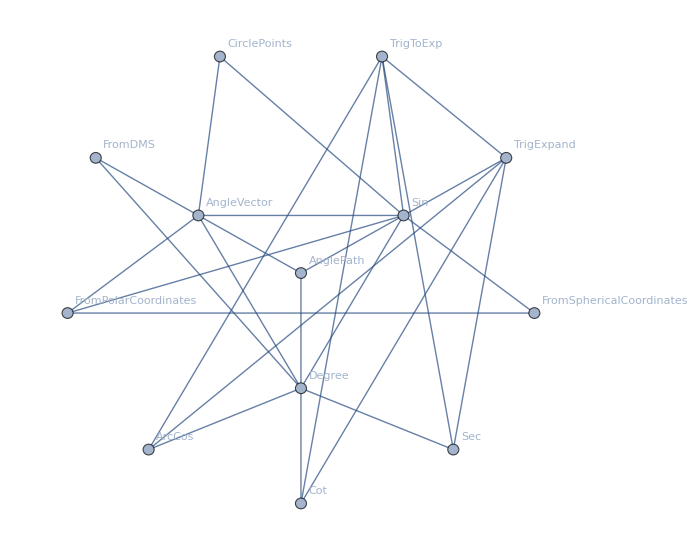

```mathematica
(* Выложить. Код "RelationshipGraph Cos" *)  
Show[WolframLanguageData["Cos", "RelationshipGraph"], AspectRatio -> 0.8, ImageSize -> 700]
```

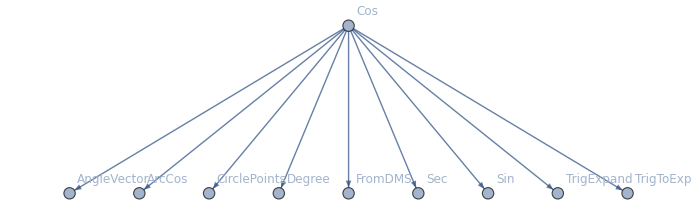

```mathematica
(* Выложить. Код "NestGraph Cos" *)  
fNestGr = WolframLanguageData[#1, EntityProperty["WolframLanguageSymbol", "RelatedSymbols"]] & ; 
grCos = NestGraph[fNestGr, Entity["WolframLanguageSymbol", "Cos"], 1, VertexLabels -> "Name", VertexLabelStyle -> 12, AspectRatio -> 0.3, ImageSize -> 700]
```

```mathematica
(* Выложить. Код "... DensityPlot ..." *)  
fXY = E^(-(x - 9)^2 - (y - 2)^2) - (2/3)*E^(-(x - 7)^2 - (3*y - 3)^2); 
xMin := 5; xMax := 11; yMin := 0; yMax := 4; aspRat = (yMax - yMin)/(xMax - xMin); 
DensityPlot[fXY, {x, xMin, xMax}, {y, yMin, yMax}, ColorFunction -> ColorData["BrownCyanTones"], AspectRatio -> aspRat, 
  ImageSize -> 600]
```

```mathematica
(* Выложить. Код "Те же функции, но графики с оформлением" *)  
Plot[{f1[x], f2[x], f3[x]}, {x, -5, 5}, PlotRange -> {{-5.01, 5.01}, {-1.1, 1.1}}, AspectRatio -> 1/2, 
  PlotStyle -> {{Blue, Thick}, {Blue, Thick, Dashed}, {Red, Thick}}, 
  GridLines -> {{-4, -2, -1, 0, 1, 2, 3, 4, 5}, {-1, -0.5, 0.5, 1}}, GridLinesStyle -> Directive[Gray, Dashed], 
  PlotLegends -> Placed[LineLegend[{"f1", "f2", "f3"}, LegendFunction -> "Frame", LegendLayout -> "Row", 
     LabelStyle -> {12, Black}, LegendLabel -> "Легенда (типы и вид линий):"], 
    {{0.18, 0.99}, {0.5, 1}}], Frame -> True, FrameLabel -> {Style["Ось абсцисс", Black, 14], 
    Style["Ось ординат: f1,f2,f3", Black, 14]}, ImageSize -> 640]
```

-     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -    <  <  <  <         >  >  >  >  -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -     -

Шаблон для текста. Шаблон для текста. Шаблон для текста. Шаблон для текста. Шаблон для текста. Шаблон для текста.